# Generate the Data

## Rb Spin Filter Magnets (Double Coil and Big Hoop)

## Create functions to represent all wires in the magnet

```mathematica
mu=1.256*^-6;

(* This is a bare-bones Biot-Savart Law. 
You give it:
1. a number representing the current
2. a vector for the direction of the current
3. a list of 3 points representing the {x,y,z} coordinates of where the current is located.
4. a list of 3 points representing the {x,y,z} coordinates of where the field is measured. 
*)
dB[current_,vectorlength_,sourcePoint_List,measurePoint_List]:=mu/(4π)current*Cross[vectorlength,measurePoint-sourcePoint]/(Norm[measurePoint-sourcePoint])^3;

 (* This function uses the dB function to make the magnetic field that results from a loop of wire. The path variable is passed in as the points on a circle. *)
circleCoildB[current_,circleRadius_,coilPosition_List,measurePoint_List,pathVariable_]:=dB[current,{-Sin[pathVariable],Cos[pathVariable],0},{circleRadius*Cos[pathVariable],circleRadius*Sin[pathVariable],0}+coilPosition,measurePoint];

(* My magnets have a significant thickness along the hoop axis, which I simulate by placing 4 wires side by side.
There are also two groups of wires at different radii. *)
rc1=8.4/2;
rc2=9.8/2;
rHoop=11.5/2;
myMagnet[current_,coilPosition_,measurePoint_List]:=circleCoildB[current,rc1,{0,0,-1.5}+coilPosition,measurePoint,θ]+ circleCoildB[current,rc1,{0,0,-.5}+coilPosition,measurePoint,θ]+
circleCoildB[current,rc1,{0,0,.5}+coilPosition,measurePoint,θ]+ circleCoildB[current,rc1,{0,0,1.5}+coilPosition,measurePoint,θ]+
circleCoildB[current,rc2,{0,0,-1.5}+coilPosition,measurePoint,θ]+ circleCoildB[current,rc2,{0,0,-.5}+coilPosition,measurePoint,θ]+
circleCoildB[current,rc2,{0,0,.5}+coilPosition,measurePoint,θ]+ circleCoildB[current,rc2,{0,0,1.5}+coilPosition,measurePoint,θ];

myHoopMagnet[current_,coilPosition_,measurePoint_List]:=circleCoildB[current,rHoop,{0,0,-.5}+coilPosition,measurePoint,θ]+
circleCoildB[current,rHoop,{0,0,.5}+coilPosition,measurePoint,θ]+ circleCoildB[current,rHoop,{0,0,0}+coilPosition,measurePoint,θ];
```

## Create an array of points to measure the field at

```mathematica
(* These variables define the area over which we find the magnetic field, as well as the number of data points to sample in that area. *)
(* Regular Run *)
width=2; (* parallel to coil radius *)
height=width; (* perpendicular to coil radius *)
dataPointSpacing=1;
array=N[Flatten[Table[{i,j},{i,-width/2,width/2,dataPointSpacing},{j,-height/2,height/2,dataPointSpacing}],1]];
(* Test Run *)

width=2;
height=2;
dataPointSpacing=1;
array=N[Flatten[Table[{i,j},{i,-width/2,width/2,dataPointSpacing},{j,-height/2,height/2,dataPointSpacing}],1]];
```

### Evaluate the field at each of the points

```mathematica
(* Here we calculate the field from each of the magnets. *)
start=AbsoluteTime[];

(* These variables define the area over which we find the magnetic field, as well as the number of data points to sample in that area. *)
(* Regular Run *)
width=2; (* parallel to coil radius *)
height=width; (* perpendicular to coil radius *)
dataPointSpacing=1;
array=N[Flatten[Table[{i,j},{i,-width/2,width/2,dataPointSpacing},{j,-height/2,height/2,dataPointSpacing}],1]];

(* Test Run *)

width=2;
height=2;
dataPointSpacing=1;
array=N[Flatten[Table[{i,j},{i,-width/2,width/2,dataPointSpacing},{j,-height/2,height/2,dataPointSpacing}],1]];

wideHoopMagnet=Apply[NIntegrate[
myHoopMagnet[1000000*50*5.868,{0,0,0},{0,#1,#2}]
,{θ,0,2π}]&,array,{1}];
end=AbsoluteTime[];
end-start


(* This is where we actually make the magnet a circle, integrating over 2π *)
arrayPiece=Take[array,{1,Floor[Length[array]/2]}];
doubleCoilMagnet1=Apply[NIntegrate[
myMagnet[100000000*173*6.22,{0,0,0},{0,#1,#2}]
,{θ,0,2π}]&,arrayPiece,{1}];
end=AbsoluteTime[];
Echo["Double Coil Finished"];
Echo[end-start];
start=end;

(* This is where we actually make the magnet a circle, integrating over 2π *)
arrayPiece=Take[array,{Floor[Length[array]/2]+1,-1}];
doubleCoilMagnet2=Apply[NIntegrate[
myMagnet[100000000*173*6.22,{0,0,0},{0,#1,#2}]
,{θ,0,2π}]&,arrayPiece,{1}];
end=AbsoluteTime[];
Echo["Double Coil Finished"];
Echo[end-start];
start=end;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 3.747×10^-16 and 5.40073×10^-13 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained -3.747×10^-16 and 5.40073×10^-13 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {3.19058}. NIntegrate obtained 5.15213×10^-16 and 1.74926×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

1.294256

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 1.98952×10^-13 and 8.47765×10^-10 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained -1.98952×10^-13 and 8.47765×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained 5.68434×10^-14 and 8.94703×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Double Coil Finished

2.896331

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {6.2831851944895132038567525704797641326881940671000847942195832729}. NIntegrate obtained -5.68434×10^-14 and 8.94703×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {6.2831611214131084832670761514128443536719714757055044174194335938}. NIntegrate obtained 9.9476×10^-14 and 7.08267×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.1269×10^-7}. NIntegrate obtained 1.42109×10^-13 and 8.47838×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Double Coil Finished

1.670053

```mathematica
(* Then export the data for later examination *)
dc1="magnetDoubleCoil_"~~ToString[height]~~"x"~~ToString[width]~~"part1.csv";
dc2="magnetDoubleCoil_"~~ToString[height]~~"x"~~ToString[width]~~"part2.csv";
bh="magnetBigHoop_"~~ToString[height]~~"x"~~ToString[width]~~".csv";
pos="positions_"~~ToString[height]~~"x"~~ToString[width]~~".csv";
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export[dc1,doubleCoilMagnet1]
Export[dc2,doubleCoilMagnet2]
Export[bh,wideHoopMagnet]
Export[pos,array]
```

C:\Users\karla\Box Sync\Gay Group\Project - Rb Spin Filter\karl\mathematicaRb\theory

magnetDoubleCoil_2x2part1.csv

magnetDoubleCoil_2x2part2.csv

magnetBigHoop_2x2.csv

positions_2x2.csv

## Rectangular Coils

## Create functions to quickly organize the four wires in a rectangular coil

```mathematica
Clear[Rectangle2D]
Rectangle2D[length_,width_,position_List:{0,0,0},eulerRotation_:{0,0,0}]:=Module[
{point1={length/2,width/2,0},point2={length/2,-width/2,0},point3={-length/2,-width/2,0},point4={-length/2,width/2,0},
points},
points={point1,point2,point3,point4,point1};
points=Map[EulerMatrix[eulerRotation].#&,points];
points=Map[position+#&,points];
points
];

(* As long as we're making these pretty pictures using the general functions, let's make a structure for rectangular coils *)
(* TODO *)
Clear[rectangleCoil]
rectangleCoil[current_, length_,width_,coilCenter_List,measurePoint_List]:=Module[{rect,currentDirections},
rect=Rectangle2D[length,width,coilCenter];
currentDirections=Map[Normalize,Differences[rect]];
NIntegrate[
dB[current,currentDirections[[1]],rect[[1]]+x*currentDirections[[1]],measurePoint]+
dB[current,currentDirections[[3]],rect[[3]]+x*currentDirections[[3]],measurePoint],{x,0,width}]+
NIntegrate[
dB[current,currentDirections[[2]],rect[[2]]+y*currentDirections[[2]],measurePoint]+
dB[current,currentDirections[[4]],rect[[4]]+y*currentDirections[[4]],measurePoint],{y,0,length}]
];
```

## Evaluate the function at an array of point

### Make the array

```mathematica
(* These variables define the area over which we find the magnetic field, as well as the number of data points to sample in that area. *)
(* Regular Run *)
width=2; (* parallel to coil radius *)
height=width; (* perpendicular to coil radius *)
dataPointSpacing=1;
array=N[Flatten[Table[{i,j},{i,-width/2,width/2,dataPointSpacing},{j,-height/2,height/2,dataPointSpacing}],1]];

(* Test Run *)

width=2;
height=2;
dataPointSpacing=1;
array=N[Flatten[Table[{i,j},{i,-width/2,width/2,dataPointSpacing},{j,-height/2,height/2,dataPointSpacing}],1]];
```

### Evaluate the array

```mathematica
(* 3D array *)
width=200; (*X*)
height=100; (*Y*)
depth=100; (*Z*)
dataPointSpacing=5;
array=N[Flatten[Table[{i,j,k},{i,-width/2,width/2,dataPointSpacing},{j,-height/2,height/2,dataPointSpacing},{k,-depth/2,depth/2,dataPointSpacing}],2]]
rectValues=Apply[rectangleCoil[100*173*6.22,183 (*X*),81 (*Y*),{0,0,0},{#1,#2,#3}]&,array,{1}];
```

{{-100.,-50.,-50.},{-100.,-50.,-45.},{-100.,-50.,-40.},{-100.,-50.,-35.},{-100.,-50.,-30.},{-100.,-50.,-25.},{-100.,-50.,-20.},{-100.,-50.,-15.},{-100.,-50.,-10.},{-100.,-50.,-5.},{-100.,-50.,0.},{-100.,-50.,5.},{-100.,-50.,10.},{-100.,-50.,15.},{-100.,-50.,20.},{-100.,-50.,25.},{-100.,-50.,30.},{-100.,-50.,35.},{-100.,-50.,40.},18043,{100.,50.,-40.},{100.,50.,-35.},{100.,50.,-30.},{100.,50.,-25.},{100.,50.,-20.},{100.,50.,-15.},{100.,50.,-10.},{100.,50.,-5.},{100.,50.,0.},{100.,50.,5.},{100.,50.,10.},{100.,50.,15.},{100.,50.,20.},{100.,50.,25.},{100.,50.,30.},{100.,50.,35.},{100.,50.,40.},{100.,50.,45.},{100.,50.,50.}}
 |  |  |  |

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {169.058}. NIntegrate obtained -9.31736×10^-21 and 1.22252×10^-20 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {182.99999671786166475385505540587720296752394233408267609775066376}. NIntegrate obtained -4.10811×10^-20 and 7.44545×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {182.99999671786166475385505540587720296752394233408267609775066376}. NIntegrate obtained -1.65171×10^-20 and 7.99712×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
Export[FileNameJoin[{$HomeDirectory,"Box Sync","Gay Group","Project - Valhalla","Magnets","rectangleCoilData.csv"}],rectValues]
```

C:\Users\karla\Box Sync\Gay Group\Project - Valhalla\Magnets\rectangleCoilData.csv

# Plot the Data

## Magnetic Field Results Overview - (3D fields, 2D points)

## Details

```mathematica
(* Functions to be used *)
NumberToCoordAxis[number_Integer]:=Switch[number,1,"X",2,"Y",3,"Z"];
VectorPlotToContour[vectorPlotData_]:=Map[{#[[1]][[1]],#[[1]][[2]],Norm[#[[2]]]}&,vectorPlotData];
VectorPlotToContourX[vectorPlotData_]:=Map[{#[[1]][[1]],#[[1]][[2]],#[[2]][[1]]}&,vectorPlotData];
VectorPlotToContourZ[vectorPlotData_]:=Map[{#[[1]][[1]],#[[1]][[2]],#[[2]][[2]]}&,vectorPlotData];
VectorPlotToContourY[vectorPlotData_]:=Map[{#[[1]][[1]],#[[1]][[2]],#[[2]][[1]]}&,vectorPlotData];

colorDiv=colorMap["piyg-11"];
contoursDiv=FindDivisions[{-max,max},numberContours*2];
GenerateOneAxisContourPlots[contourData_]:=Map[ListContourPlot[#,ColorFunction->(Blend[colorDiv,(#1+max)/(2*max)]&),ColorFunctionScaling->False,PlotRange->plotLimits,Contours->contoursDiv]&,contourData];

PlotMagnetData[positionData_,fieldData_]:=Module[{},
fields2DSubsets=Subsets[{1,2,3},{2}][[{1,3}]];

field2DValues=Map[fieldData[[All,#]]&,fields2DSubsets];
positionValues=positionData;
vectorPlotData=Map[Transpose[{positionValues,#}]&,field2DValues];

(* Compute the magnitude of the field and organize the data for contour map plotting *)
contourDataMag=Map[VectorPlotToContour,vectorPlotData];
contourDataX=Map[VectorPlotToContourX,vectorPlotData];
contourDataY=Map[VectorPlotToContourY,vectorPlotData];
contourDataZ=Map[VectorPlotToContourZ,vectorPlotData];

(* Set Plotting Parameters *)
plotLimits={{-20,20},{-20,20},Full};
allContourData=Flatten[contourDataMag,1];
justIntensity=allContourData[[All,3]];
max=Max[justIntensity];
min=Min[justIntensity];

(* Generate Vector Plot *)
plots=Map[ListVectorPlot[#,PlotRange->plotLimits]&,vectorPlotData];

(* First a plot of the MAGNITUDE of the field at a number of locations *)
numberContours=8;
colorSeq=tolIridescentPalette[[;;-2]];
contoursSeq=FindDivisions[{min,max},numberContours];
listContourPlots=Map[ListContourPlot[#,ColorFunction->(Blend[colorSeq,(#1-min)/max]&),ColorFunctionScaling->False,PlotRange->plotLimits,Contours->contoursSeq]&,contourDataMag];
(* The legend of what the colors mean. *)
seqBarLegend=BarLegend[{(Blend[colorSeq,(#1-min)/max])&,{min,max}},contoursSeq];

(* Then a plots of each COMPONENT of the field *)
colorDiv=colorMap["piyg-11"];
contoursDiv=FindDivisions[{-max,max},numberContours*2];
listContourPlotsComponents=Map[GenerateOneAxisContourPlots[#]&,{contourDataX,contourDataY,contourDataZ}];
(* The legend of what the colors mean *)
divBarLegend=BarLegend[{(Blend[colorDiv,(#1+max)/max/2])&,{-max,max}},contoursDiv];

GraphicsGrid[Join[{{"X-Y","Y-Z"}},{plots},{listContourPlots},listContourPlotsComponents,{{seqBarLegend,divBarLegend}}],ImageSize->Full]
];
```

FindDivisions::fdargs: The arguments in FindDivisions[{-max,max}, 2 numberContours, 10] are not supported.

```mathematica
(* Set directory to location of files *)
SetDirectory[NotebookDirectory[]];
(* Show just the folders where the Notebook is located. *)
Select[FileNames[],DirectoryQ]
FileNames[FileNameJoin[{"2020-04-09","*"}]]
```

{2020-03-26,2020-04-03,2020-04-09,2020-04-13}

{2020-04-09\job.26393717.err,2020-04-09\job.26393717.out,2020-04-09\magnetBigHoop_90x30.csv,2020-04-09\magnetDoubleCoil_90x30_part1.csv,2020-04-09\magnetDoubleCoil_90x30_part2.csv,2020-04-09\positions_90x30.csv}

```mathematica
(* Import the files, if you didn't just calculate them from the code above.*)
dc1=Import[FileNameJoin[{"2020-04-09","magnetDoubleCoil_90x30_part1.csv"}]];
dc2=Import[FileNameJoin[{"2020-04-09","magnetDoubleCoil_90x30_part2.csv"}]];
dc=Join[dc1,dc2];
bh=Import[FileNameJoin[{"2020-04-09","magnetBigHoop_90x30.csv"}]];
pos=Import[FileNameJoin[{"2020-04-09","positions_90x30.csv"}]];
```

```mathematica
(* If 2D data was collected, likely only two of the field components will
be interesting. In our case, X was always 0 and so the mangetic field cancels out 
there. We take only the {X,Y} and {Y,Z} data, leaving {X,Z} out. 

TODO: write a function to manipulate the data so that the Y axis is duplicated. 
Due to symmetry, the X data will be identical to the Y data.*)
fields2DSubsets=Subsets[{1,2,3},{2}][[{1,3}]]


field2DValues=Map[dc[[All,#]]&,fields2DSubsets]
positionValues=pos;
vectorPlotData=Map[Transpose[{positionValues,#}]&,field2DValues];

(* Compute the magnitude of the field and organize the data for contour map plotting *)
contourDataMag=Map[VectorPlotToContour,vectorPlotData];
contourDataX=Map[VectorPlotToContourX,vectorPlotData];
contourDataY=Map[VectorPlotToContourY,vectorPlotData];
contourDataZ=Map[VectorPlotToContourZ,vectorPlotData];
```

{{1,2},{2,3}}

{{{2.7478×10^-15,0.52034},{3.05311×10^-15,0.535533},{2.22045×10^-15,0.551297},{1.05471×10^-15,0.567656},{1.9984×10^-15,0.584638},{1.22125×10^-15,0.602271},{1.41553×10^-15,0.620584},{2.55004×10^-15,0.63961},11026,{-5.55112×10^-17,0.620584},{-2.94209×10^-15,0.602271},{-6.66134×10^-16,0.584638},{-1.05471×10^-15,0.567656},{-1.60982×10^-15,0.551297},{-4.44089×10^-16,0.535533},{-1.7486×10^-15,0.52034}},{1}}
 |  |  |  |

```mathematica
(* Set Plotting Parameters *)
plotLimits={{-20,20},{-20,20},Full};
allContourData=Flatten[contourDataMag,1];
justIntensity=allContourData[[All,3]];
max=Max[justIntensity];
min=Min[justIntensity];

(* Generate Vector Plot *)
plots=Map[ListVectorPlot[#,PlotRange->plotLimits]&,vectorPlotData];
```

General::prng: Value of option PlotRange -> {{-20,20},{-20,20},Full} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

```mathematica
(* First a plot of the MAGNITUDE of the field at a number of locations *)
numberContours=8;
colorSeq=tolIridescentPalette[[;;-2]];
contoursSeq=FindDivisions[{min,max},numberContours];
listContourPlots=Map[ListContourPlot[#,ColorFunction->(Blend[colorSeq,(#1-min)/max]&),ColorFunctionScaling->False,PlotRange->plotLimits,Contours->contours]&,contourDataMag];
(* The legend of what the colors mean. *)
seqBarLegend=BarLegend[{(Blend[colorSeq,(#1-min)/max])&,{min,max}},contoursSeq];

(* Then a plots of each COMPONENT of the field *)
colorDiv=colorMap["piyg-11"];
contoursDiv=FindDivisions[{-max,max},numberContours*2];
listContourPlotsComponents=Map[GenerateOneAxisContourPlots[#]&,{contourDataX,contourDataY,contourDataZ}];
(* The legend of what the colors mean *)
divBarLegend=BarLegend[{(Blend[colorDiv,(#1+max)/max/2])&,{-max,max}},contoursDiv];
```

Contours::ilevels: contours is not a valid contour specification.

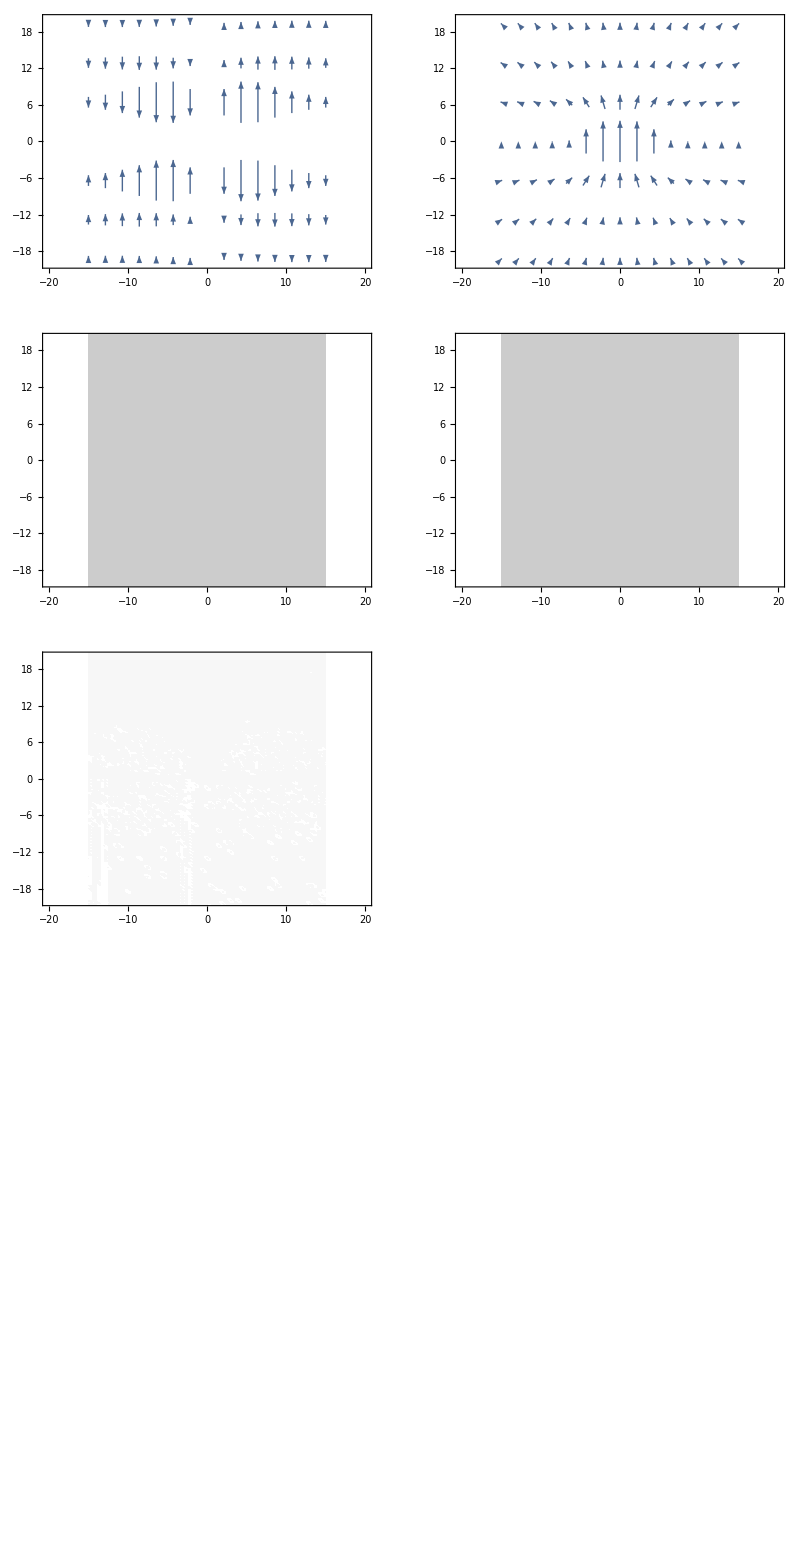

```mathematica
GraphicsGrid[Join[{{"X-Y","Y-Z"}},{plots},{listContourPlots},listContourPlotsComponents,{{seqBarLegend,divBarLegend}}],ImageSize->Full]
```

## Just Plot

```mathematica
(* Load in the data *)
SetDirectory[NotebookDirectory[]];
dateFolder="2020-04-09";
FileNames[FileNameJoin[{dateFolder,"*"}]];
(* Import the files, if you didn't just calculate them from the code above.*)
dc1=Import[FileNameJoin[{dateFolder,"magnetDoubleCoil_90x30_part1.csv"}]];
dc2=Import[FileNameJoin[{dateFolder,"magnetDoubleCoil_90x30_part2.csv"}]];
dc=Join[dc1,dc2];
bh=Import[FileNameJoin[{dateFolder,"magnetBigHoop_90x30.csv"}]];
pos=Import[FileNameJoin[{dateFolder,"positions_90x30.csv"}]];
(* Plot the data *)
PlotMagnetData[pos,dc]
```

General::prng: Value of option PlotRange -> {{-20,20},{-20,20},Full} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics-

```mathematica
PlotMagnetData[pos,bh]
```

General::prng: Value of option PlotRange -> {{-20,20},{-20,20},Full} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics-

## Superimpose field data

```mathematica
(* Later Examination *)
SetDirectory[NotebookDirectory[]];
(* Show just the folders where the Notebook is located. *)
Select[FileNames[],DirectoryQ]
FileNames[FileNameJoin[{"2020-04-09","*"}]]
```

{2020-03-26,2020-04-03,2020-04-09,2020-04-13,img}

{2020-04-09\job.26393717.err,2020-04-09\job.26393717.out,2020-04-09\magnetBigHoop_90x30.csv,2020-04-09\magnetDoubleCoil_90x30_part1.csv,2020-04-09\magnetDoubleCoil_90x30_part2.csv,2020-04-09\positions_90x30.csv}

```mathematica
(* Import the files, if you didn't just calculate them from the code above.*)
dc1=Import[FileNameJoin[{"2020-04-09","magnetDoubleCoil_90x30_part1.csv"}]]
dc2=Import[FileNameJoin[{"2020-04-09","magnetDoubleCoil_90x30_part2.csv"}]]
dc=Join[dc1,dc2];
bh=Import[FileNameJoin[{"2020-04-09","magnetBigHoop_90x30.csv"}]]
pos=Import[FileNameJoin[{"2020-04-09","positions_90x30.csv"}]]
```

{{2.7478×10^-15,0.52034,1.57319},{3.05311×10^-15,0.535533,1.60139},{2.22045×10^-15,0.551297,1.63027},{1.05471×10^-15,0.567656,1.65985},{1.9984×10^-15,0.584638,1.69015},5510,{9.32587×10^-15,6.96665×10^-15,145.983},{1.19627×10^-14,4.16334×10^-15,157.305},{-4.996×10^-16,1.68268×10^-16,167.153},{4.94049×10^-15,-3.60822×10^-16,174.807},{3.60476×10^-15,3.46077×10^-16,179.663}}
 |  |  |  |

{{0.,0.,181.328},{-3.60476×10^-15,-3.46077×10^-16,179.663},{-4.94049×10^-15,3.60822×10^-16,174.807},{4.996×10^-16,-1.68268×10^-16,167.153},{-1.19627×10^-14,-4.16334×10^-15,157.305},{-9.32587×10^-15,-6.96665×10^-15,145.983},5510,{-6.66134×10^-16,0.584638,1.69015},{-1.05471×10^-15,0.567656,1.65985},{-1.60982×10^-15,0.551297,1.63027},{-4.44089×10^-16,0.535533,1.60139},{-1.7486×10^-15,0.52034,1.57319}}
 |  |  |  |

{{3.13985×10^-16,0.0704695,0.214476},{1.94289×10^-16,0.0725138,0.218309},{8.67362×10^-17,0.0746342,0.222235},{3.4521×10^-16,0.0768343,0.226256},{1.249×10^-16,0.0791175,0.230374},11031,{-2.60209×10^-16,0.0791175,0.230374},{-3.00107×10^-16,0.0768343,0.226256},{-2.15973×10^-16,0.0746342,0.222235},{-3.97252×10^-16,0.0725138,0.218309},{-3.46945×10^-16,0.0704695,0.214476}}
 |  |  |  |

{{-15.,-45.},{-15.,-44.5},{-15.,-44.},{-15.,-43.5},{-15.,-43.},{-15.,-42.5},{-15.,-42.},{-15.,-41.5},{-15.,-41.},{-15.,-40.5},{-15.,-40.},{-15.,-39.5},{-15.,-39.},{-15.,-38.5},{-15.,-38.},{-15.,-37.5},{-15.,-37.},{-15.,-36.5},{-15.,-36.},{-15.,-35.5},{-15.,-35.},{-15.,-34.5},{-15.,-34.},{-15.,-33.5},{-15.,-33.},{-15.,-32.5},{-15.,-32.},{-15.,-31.5},10986,{15.,32.},{15.,32.5},{15.,33.},{15.,33.5},{15.,34.},{15.,34.5},{15.,35.},{15.,35.5},{15.,36.},{15.,36.5},{15.,37.},{15.,37.5},{15.,38.},{15.,38.5},{15.,39.},{15.,39.5},{15.,40.},{15.,40.5},{15.,41.},{15.,41.5},{15.,42.},{15.,42.5},{15.,43.},{15.,43.5},{15.,44.},{15.,44.5},{15.,45.}}
 |  |  |  |

```mathematica
mag2Loc=-5.91/2-4.2/2+(* Fudge Factor *).055
mag3Loc=5.91/2+4.2/2-(*Fudge Factor *) .055
mag1Loc=mag2Loc-8.66-4.2-.14(* Fudge Factor *)
mag4Loc=mag3Loc+4.2/2+8.68+.5+(*Fudge Factor*).22
mag1Pos=Map[#+{0,mag1Loc}&,pos];
mag2Pos=Map[#+{0,mag2Loc}&,pos];
mag3Pos=Map[#+{0,mag3Loc}&,pos];
mag4Pos=Map[#+{0,mag4Loc}&,pos];
```

-5.

5.

-18.

16.5

```mathematica
(* 

STOP!

Only evaluate if not loading in files *)
pos=array;
bh=wideHoopMagnet;
```

```mathematica
(* Modify the end result so we can view them in a vector field plot *)
yNzBigHoop=bh[[All,{2,3}]]; (* The program was run so that there were 2 A of current in the Big Hoop Coil. I'm comfortable putting in as much as 3 A for a period of time. *)
yNzDoubleCoil=dc[[All,{2,3}]];
listVectorData=Transpose[{mag1Pos,yNzDoubleCoil}]
listVectorData2=Transpose[{mag2Pos,yNzDoubleCoil}];
listVectorData3=Transpose[{mag3Pos,yNzDoubleCoil}];
listVectorData4=Transpose[{mag4Pos,yNzBigHoop}];
```

{{{-15.,-63.},{0.52034,1.57319}},{{-15.,-62.5},{0.535533,1.60139}},{{-15.,-62.},{0.551297,1.63027}},{{-15.,-61.5},{0.567656,1.65985}},{{-15.,-61.},{0.584638,1.69015}},{{-15.,-60.5},{0.602271,1.72119}},11029,{{15.,24.5},{0.602271,1.72119}},{{15.,25.},{0.584638,1.69015}},{{15.,25.5},{0.567656,1.65985}},{{15.,26.},{0.551297,1.63027}},{{15.,26.5},{0.535533,1.60139}},{{15.,27.},{0.52034,1.57319}}}
 |  |  |  |

```mathematica
(* This function adds together the fields from different magnets. It assumes that the positions that fields were recorded are the same between magnets. *)

AssociationSumOnKeys[data1_,data2_]:=Module[
{keys1=data1[[All,1]],keys2=data2[[All,1]],
values1=data1[[All,2]],values2=data2[[All,2]],
map1,map2,allKeys},
map1=AssociationThread[keys1,values1];
map2=AssociationThread[keys2,values2];
allKeys=DeleteDuplicates[Join[keys1,keys2]];
Map[{#,If[KeyExistsQ[map1,#],map1[#],0]+If[KeyExistsQ[map2,#],map2[#],0]}&,allKeys]
];
```

```mathematica
listVectorDataSum=AssociationSumOnKeys[listVectorData,listVectorData2];
listVectorDataSum=AssociationSumOnKeys[listVectorDataSum,listVectorData3];
listVectorDataSum=AssociationSumOnKeys[listVectorDataSum,listVectorData4];
```

```mathematica
(* Plot a vector Field *)
axesLabel={"Y Axis","Z Axis"}
ListVectorPlot[listVectorDataSum,VectorPoints->All,FrameLabel->axesLabel]
ListVectorPlot[listVectorDataSum,FrameLabel->axesLabel]
```

{Y Axis,Z Axis}

-Graphics-

-Graphics-

```mathematica
(* Compute the magnitude of the field and organize the data for contour map plotting *)
contourData=Map[{#[[1]][[1]],#[[1]][[2]],Norm[#[[2]]]}&,listVectorDataSum];
```

```mathematica
contours=8;
max=Max[contourData[[All,3]]]
max=250
min=Min[contourData[[All,3]]]
min=25
color=tolIridescentPalette[[3;;-2]]
plot=ListContourPlot[contourData,ColorFunction->(Blend[color,#1]&),PlotLegends->BarLegend[{(Blend[color,#1])&,{min,max}},contours],FrameLabel->axesLabel,PlotRange->{{-15,15},{-36,24},{max,min}},Contours->contours,AspectRatio->2]
```

237.069

250

0.225756

25

{RGBColor[0.9607843137254902, 0.9529411764705882, 0.7568627450980392],RGBColor[0.9176470588235294, 0.9411764705882353, 0.7098039215686275],RGBColor[0.8666666666666667, 0.9254901960784314, 0.7490196078431373],RGBColor[0.8666666666666667, 0.9058823529411765, 0.792156862745098],RGBColor[0.7607843137254902, 0.8901960784313725, 0.8235294117647058],RGBColor[0.7098039215686275, 0.8666666666666667, 0.8470588235294118],RGBColor[0.6588235294117647, 0.8470588235294118, 0.8627450980392157],RGBColor[0.596078431372549, 0.8235294117647058, 0.8823529411764706],RGBColor[0.5529411764705883, 0.796078431372549, 0.8941176470588236],RGBColor[0.5058823529411764, 0.7686274509803922, 0.9058823529411765],RGBColor[0.4823529411764706, 0.7372549019607844, 0.9058823529411765],RGBColor[0.49411764705882355, 0.6980392156862745, 0.8941176470588236],RGBColor[0.5333333333333333, 0.6470588235294118, 0.8666666666666667],RGBColor[0.5764705882352941, 0.596078431372549, 0.8235294117647058],RGBColor[0.6078431372549019, 0.5411764705882353, 0.7686274509803922],RGBColor[0.615686274509804, 0.49019607843137253, 0.6980392156862745],RGBColor[0.6039215686274509, 0.4392156862745098, 0.6196078431372549],RGBColor[0.5647058823529412, 0.38823529411764707, 0.5333333333333333],RGBColor[0.5019607843137255, 0.3411764705882353, 0.4392156862745098],RGBColor[0.40784313725490196, 0.28627450980392155, 0.3411764705882353],RGBColor[0.27450980392156865, 0.20784313725490197, 0.22745098039215686]}

-Graphics-

```mathematica
extNames={".eps",".png",".pdf",".svg"}
fileName="rbSpinFilterMagneticFields.ext"
Map[Export[StringReplace[fileName,".ext"->#],plot]&,extNames];
```

{.eps,.png,.pdf,.svg}

rbSpinFilterMagneticFields.ext

```mathematica
contours=4;
max=Max[contourData[[All,3]]]
max=50
min=Min[contourData[[All,3]]]
min=0
color=tolIridescentPalette[[;;-2]]
ListContourPlot[contourData,ColorFunction->(Blend[color,#1]&),PlotLegends->BarLegend[{(Blend[color,#1])&,{min,max}},contours],FrameLabel->axesLabel,PlotRange->{{-15,15},{-36,24},{min,max}},Contours->contours,AspectRatio->2]
```

237.069

50

0.225756

0

{RGBColor[0.996078431372549, 0.984313725490196, 0.9137254901960784],RGBColor[0.9882352941176471, 0.9686274509803922, 0.8352941176470589],RGBColor[0.9607843137254902, 0.9529411764705882, 0.7568627450980392],RGBColor[0.9176470588235294, 0.9411764705882353, 0.7098039215686275],RGBColor[0.8666666666666667, 0.9254901960784314, 0.7490196078431373],RGBColor[0.8666666666666667, 0.9058823529411765, 0.792156862745098],RGBColor[0.7607843137254902, 0.8901960784313725, 0.8235294117647058],RGBColor[0.7098039215686275, 0.8666666666666667, 0.8470588235294118],RGBColor[0.6588235294117647, 0.8470588235294118, 0.8627450980392157],RGBColor[0.596078431372549, 0.8235294117647058, 0.8823529411764706],RGBColor[0.5529411764705883, 0.796078431372549, 0.8941176470588236],RGBColor[0.5058823529411764, 0.7686274509803922, 0.9058823529411765],RGBColor[0.4823529411764706, 0.7372549019607844, 0.9058823529411765],RGBColor[0.49411764705882355, 0.6980392156862745, 0.8941176470588236],RGBColor[0.5333333333333333, 0.6470588235294118, 0.8666666666666667],RGBColor[0.5764705882352941, 0.596078431372549, 0.8235294117647058],RGBColor[0.6078431372549019, 0.5411764705882353, 0.7686274509803922],RGBColor[0.615686274509804, 0.49019607843137253, 0.6980392156862745],RGBColor[0.6039215686274509, 0.4392156862745098, 0.6196078431372549],RGBColor[0.5647058823529412, 0.38823529411764707, 0.5333333333333333],RGBColor[0.5019607843137255, 0.3411764705882353, 0.4392156862745098],RGBColor[0.40784313725490196, 0.28627450980392155, 0.3411764705882353],RGBColor[0.27450980392156865, 0.20784313725490197, 0.22745098039215686]}

-Graphics-

```mathematica
(* Compute the magnitude of the field and organize the data for contour map plotting *)
contourDataComponent=Map[{#[[1]][[1]],#[[1]][[2]],#[[2]][[1]]}&,listVectorDataSum];
```

```mathematica
contours=5;
max=Max[contourDataComponent[[All,3]]]
min=Min[contourDataComponent[[All,3]]]
color=colorMap["piyg-11"];
ListContourPlot[contourDataComponent,ColorFunction->(Blend[color,#1]&),PlotLegends->BarLegend[{(Blend[color,#1])&,{min,max}},contours],FrameLabel->axesLabel,PlotRange->{{-15,15},{-36,24},Full},Contours->contours,AspectRatio->2]
```

63.6781

-63.6781

-Graphics-

```mathematica
(* Compute the magnitude of the field and organize the data for contour map plotting *)
contourDataComponent=Map[{#[[1]][[1]],#[[1]][[2]],#[[2]][[2]]}&,listVectorDataSum];
```

```mathematica
contours=8;
max=Max[contourDataComponent[[All,3]]]
min=Min[contourDataComponent[[All,3]]]
color=colorMap["rdylbu-11"];
ListContourPlot[contourDataComponent,ColorFunction->(Blend[color,#1]&),PlotLegends->BarLegend[{(Blend[color,#1])&,{min,max}},contours],FrameLabel->axesLabel,PlotRange->{{-15,15},{-36,24},Full},Contours->contours,AspectRatio->2]
```

237.069

0.214476

-Graphics-

```mathematica
contours=8;
max=Max[contourDataComponent[[All,3]]]
min=Min[contourDataComponent[[All,3]]]
color=colorMap["rdylbu-11"];
ListPlot3D[contourDataComponent,PlotRange->{{-15,15},{-36,24},Full},ColorFunction->(Blend[color,#3]&)]
```

237.069

0.214476

-Graphics3D-

```mathematica
x=pos[[182+181*29;;181*31]][[All,2]]
y=dc[[182+181*29;;181*31]][[All,3]]
```

{-45.,-44.5,-44.,-43.5,-43.,-42.5,-42.,-41.5,-41.,-40.5,-40.,-39.5,-39.,-38.5,-38.,-37.5,-37.,-36.5,-36.,-35.5,-35.,-34.5,-34.,-33.5,-33.,-32.5,-32.,-31.5,-31.,-30.5,-30.,-29.5,-29.,-28.5,-28.,-27.5,-27.,-26.5,-26.,-25.5,-25.,-24.5,-24.,-23.5,-23.,-22.5,-22.,-21.5,-21.,-20.5,-20.,-19.5,-19.,-18.5,-18.,-17.5,-17.,-16.5,-16.,-15.5,-15.,-14.5,-14.,-13.5,-13.,-12.5,-12.,-11.5,-11.,-10.5,-10.,-9.5,-9.,-8.5,-8.,-7.5,-7.,-6.5,-6.,-5.5,-5.,-4.5,-4.,-3.5,-3.,-2.5,-2.,-1.5,-1.,-0.5,0.,0.5,1.,1.5,2.,2.5,3.,3.5,4.,4.5,5.,5.5,6.,6.5,7.,7.5,8.,8.5,9.,9.5,10.,10.5,11.,11.5,12.,12.5,13.,13.5,14.,14.5,15.,15.5,16.,16.5,17.,17.5,18.,18.5,19.,19.5,20.,20.5,21.,21.5,22.,22.5,23.,23.5,24.,24.5,25.,25.5,26.,26.5,27.,27.5,28.,28.5,29.,29.5,30.,30.5,31.,31.5,32.,32.5,33.,33.5,34.,34.5,35.,35.5,36.,36.5,37.,37.5,38.,38.5,39.,39.5,40.,40.5,41.,41.5,42.,42.5,43.,43.5,44.,44.5,45.}

{1.9363,1.97968,2.02452,2.0709,2.11889,2.16856,2.22,2.27327,2.32848,2.38572,2.44509,2.5067,2.57065,2.63707,2.70609,2.77784,2.85248,2.93014,3.01101,3.09526,3.18307,3.27466,3.37024,3.47004,3.57431,3.68333,3.79738,3.91678,4.04187,4.17301,4.31059,4.45504,4.60682,4.76643,4.93442,5.11137,5.29794,5.49482,5.70278,5.92266,6.15538,6.40194,6.66346,6.94115,7.23636,7.55058,7.88545,8.24278,8.62462,9.03321,9.47107,9.941,10.4462,10.9901,11.5768,12.2107,12.897,13.6414,14.4504,15.3316,16.2934,17.3458,18.4998,19.7686,21.1671,22.7126,24.4253,26.3287,28.4501,30.8212,33.4793,36.4677,39.8366,43.6441,47.9569,52.8503,58.4078,64.7183,71.8719,79.9502,89.0113,99.067,110.051,121.781,133.925,145.983,157.305,167.153,174.807,179.663,181.328,179.663,174.807,167.153,157.305,145.983,133.925,121.781,110.051,99.067,89.0113,79.9502,71.8719,64.7183,58.4078,52.8503,47.9569,43.6441,39.8366,36.4677,33.4793,30.8212,28.4501,26.3287,24.4253,22.7126,21.1671,19.7686,18.4998,17.3458,16.2934,15.3316,14.4504,13.6414,12.897,12.2107,11.5768,10.9901,10.4462,9.941,9.47107,9.03321,8.62462,8.24278,7.88545,7.55058,7.23636,6.94115,6.66346,6.40194,6.15538,5.92266,5.70278,5.49482,5.29794,5.11137,4.93442,4.76643,4.60682,4.45504,4.31059,4.17301,4.04187,3.91678,3.79738,3.68333,3.57431,3.47004,3.37024,3.27466,3.18307,3.09526,3.01101,2.93014,2.85248,2.77784,2.70609,2.63707,2.57065,2.5067,2.44509,2.38572,2.32848,2.27327,2.22,2.16856,2.11889,2.0709,2.02452,1.97968,1.9363}

```mathematica
ListPlot[Transpose[{x,y}],PlotRange->Full]
```

-Graphics-

```mathematica
(* Modify the end result so we can view them in a vector field plot *)
yNzBigHoop=dc[[All,{2,3}]]; (* The program was run so that there were 2 A of current in the Big Hoop Coil. I'm comfortable putting in as much as 3 A for a period of time. *)
listVectorData=Transpose[{pos,yNzBigHoop}];
listVectorDataSum=AssociationSumOnKeys[listVectorData,listVectorData];
listVectorData;
(* Compute the magnitude of the field and organize the data for contour map plotting *)
contourData=Map[{#[[1]][[1]],#[[1]][[2]],Norm[#[[2]]]}&,listVectorData];
```

```mathematica
contours=16;
max=Max[contourData[[All,3]]]
min=Min[contourData[[All,3]]]
color=tolIridescentPalette[[;;-2]]
ListContourPlot[contourData,ColorFunction->(Blend[color,#1]&),PlotLegends->BarLegend[{(Blend[color,#1])&,{0,max}},contours],FrameLabel->axesLabel,PlotRange->{{-5,5},{-45,45},Full},Contours->contours,AspectRatio->2]
```

250.199

231.241

{RGBColor[0.996078431372549, 0.984313725490196, 0.9137254901960784],RGBColor[0.9882352941176471, 0.9686274509803922, 0.8352941176470589],RGBColor[0.9607843137254902, 0.9529411764705882, 0.7568627450980392],RGBColor[0.9176470588235294, 0.9411764705882353, 0.7098039215686275],RGBColor[0.8666666666666667, 0.9254901960784314, 0.7490196078431373],RGBColor[0.8666666666666667, 0.9058823529411765, 0.792156862745098],RGBColor[0.7607843137254902, 0.8901960784313725, 0.8235294117647058],RGBColor[0.7098039215686275, 0.8666666666666667, 0.8470588235294118],RGBColor[0.6588235294117647, 0.8470588235294118, 0.8627450980392157],RGBColor[0.596078431372549, 0.8235294117647058, 0.8823529411764706],RGBColor[0.5529411764705883, 0.796078431372549, 0.8941176470588236],RGBColor[0.5058823529411764, 0.7686274509803922, 0.9058823529411765],RGBColor[0.4823529411764706, 0.7372549019607844, 0.9058823529411765],RGBColor[0.49411764705882355, 0.6980392156862745, 0.8941176470588236],RGBColor[0.5333333333333333, 0.6470588235294118, 0.8666666666666667],RGBColor[0.5764705882352941, 0.596078431372549, 0.8235294117647058],RGBColor[0.6078431372549019, 0.5411764705882353, 0.7686274509803922],RGBColor[0.615686274509804, 0.49019607843137253, 0.6980392156862745],RGBColor[0.6039215686274509, 0.4392156862745098, 0.6196078431372549],RGBColor[0.5647058823529412, 0.38823529411764707, 0.5333333333333333],RGBColor[0.5019607843137255, 0.3411764705882353, 0.4392156862745098],RGBColor[0.40784313725490196, 0.28627450980392155, 0.3411764705882353],RGBColor[0.27450980392156865, 0.20784313725490197, 0.22745098039215686]}

-Graphics-

## Magnetic Field Results Overview-3D

```mathematica
fieldXYZValues=rectValues[[All,{1,2,3}]];

positionValues=array;
shift=4;
positionValues1=Map[#+{0,0,shift}&,positionValues];
vectorPlotData1=Transpose[{positionValues1,fieldXYZValues}];
vectorPlotData=vectorPlotData1;
ListVectorPlot3D[vectorPlotData,AxesLabel->{"X","Y","Z"}]
(* Compute the magnitude of the field and organize the data for contour map plotting *)
contourData=Map[{#[[1]][[1]],#[[1]][[2]],#[[2]][[2]]}&,vectorPlotData];
contours=8;
max=Max[contourData[[All,3]]];
min=Min[contourData[[All,3]]];
color=colorMap["rdylbu-11"];
ListContourPlot[contourData,ColorFunction->(Blend[color,#1]&),PlotLegends->BarLegend[{(Blend[color,#1])&,{min,max}},contours],FrameLabel->axesLabel,PlotRange->{{-15,15},{-30,30},Full},Contours->contours,AspectRatio->2]
```

-Graphics3D-

-Graphics-

## Adding a magnet in a new position.

```mathematica
positionValues=array;
shift=-4;
positionValues2=Map[#+{0,0,shift}&,positionValues];
vectorPlotData2=Transpose[{positionValues2,fieldXYZValues}];
vectorPlotData=vectorPlotData1;
ListVectorPlot3D[vectorPlotData,AxesLabel->{"X","Y","Z"}]
(* Compute the magnitude of the field and organize the data for contour map plotting *)
contourData=Map[{#[[1]][[1]],#[[1]][[3]],#[[2]][[3]]}&,vectorPlotData];
contours=8;
max=Max[contourData[[All,3]]];
min=Min[contourData[[All,3]]];
color=colorMap["rdylbu-11"];
ListContourPlot[contourData,ColorFunction->(Blend[color,#1]&),PlotLegends->BarLegend[{(Blend[color,#1])&,{min,max}},contours],FrameLabel->axesLabel,PlotRange->{{-15,15},{-30,30},Full},Contours->contours,AspectRatio->2]
```

-Graphics3D-

-Graphics-

```mathematica
vectorPlotData1[[All,{1,2}]]
vectorPlotData=AssociationSumOnKeys[vectorPlotData1,vectorPlotData2]
ListVectorPlot3D[vectorPlotData1[[;;100]]]
```

{{{-5.,-5.,-1.},{-0.000272286,-0.000272286,-0.0000242535}},{{-5.,-5.,0.},{-0.000311834,-0.000311834,0.0000615473}},{{-5.,-5.,1.},{-0.000325459,-0.000325459,0.000190735}},{{-5.,-5.,2.},{-0.000285996,-0.000285996,0.000351315}},{{-5.,-5.,3.},{-0.000172602,-0.000172602,0.000497064}},1322,{{5.,5.,6.},{-0.000285996,-0.000285996,0.000351315}},{{5.,5.,7.},{-0.000325459,-0.000325459,0.000190735}},{{5.,5.,8.},{-0.000311834,-0.000311834,0.0000615473}},{{5.,5.,9.},{-0.000272286,-0.000272286,-0.0000242535}}}
 |  |  |  |

{{{-5.,-5.,-1.},{0.000053173,0.000053173,0.000166482}},{{-5.,-5.,0.},{0.,0.,0.000123095}},{{-5.,-5.,1.},{-0.000053173,-0.000053173,0.000166482}},{{-5.,-5.,2.},{-0.000285996,-0.000285996,0.000351315}},{{-5.,-5.,3.},{-0.000172602,-0.000172602,0.000497064}},2652,{{5.,5.,-3.},{-0.000172602,-0.000172602,0.000497064}},{{5.,5.,-2.},{-0.000285996,-0.000285996,0.000351315}},{{5.,5.,-1.},{-0.000053173,-0.000053173,0.000166482}},{{5.,5.,0.},{0.,0.,0.000123095}},{{5.,5.,1.},{0.000053173,0.000053173,0.000166482}}}
 |  |  |  |

Visualization`Core`ListVectorPlot3D::vfldata: {{{-5.,-5.,-1.},{-0.000272286,-0.000272286,-0.0000242535}},{{-5.,-5.,0.},{-0.000311834,-0.000311834,0.0000615473}},{{-5.,-5.,1.},{-0.000325459,-0.000325459,0.000190735}},{{-5.,-5.,2.},{-0.000285996,-0.000285996,0.000351315}},{{-5.,-5.,3.},{-0.000172602,-0.000172602,0.000497064}},{{-5.,-5.,4.},{0.,0.,0.000557941}},«40»,{{-5.,-1.,1.},{-0.00116983,-0.000221734,0.0000634692}},{{-5.,-1.,2.},{-0.00129067,-0.000236067,0.000572921}},{{-5.,-1.,3.},{-0.000950367,-0.000166957,0.00126793}},{{-5.,-1.,4.},{0.,0.,0.00164219}},«50»} is not a valid vector field dataset or a valid list of datasets.

ListVectorPlot3D[{{{-5.,-5.,-1.},{-0.000272286,-0.000272286,-0.0000242535}},{{-5.,-5.,0.},{-0.000311834,-0.000311834,0.0000615473}},{{-5.,-5.,1.},{-0.000325459,-0.000325459,0.000190735}},{{-5.,-5.,2.},{-0.000285996,-0.000285996,0.000351315}},{{-5.,-5.,3.},{-0.000172602,-0.000172602,0.000497064}},{{-5.,-5.,4.},{0.,0.,0.000557941}},{{-5.,-5.,5.},{0.000172602,0.000172602,0.000497064}},{{-5.,-5.,6.},{0.000285996,0.000285996,0.000351315}},{{-5.,-5.,7.},{0.000325459,0.000325459,0.000190735}},{{-5.,-5.,8.},{0.000311834,0.000311834,0.0000615473}},{{-5.,-5.,9.},{0.000272286,0.000272286,-0.0000242535}},{{-5.,-4.,-1.},{-0.000369937,-0.000295019,-0.0000787824}},{{-5.,-4.,0.},{-0.000447089,-0.000355899,0.0000190128}},{{-5.,-4.,1.},{-0.000496287,-0.000394037,0.00018841}},{{-5.,-4.,2.},{-0.000465034,-0.000368042,0.000427279}},{{-5.,-4.,3.},{-0.000295942,-0.000233527,0.000669018}},{{-5.,-4.,4.},{0.,0.,0.000777034}},{{-5.,-4.,5.},{0.000295942,0.000233527,0.000669018}},{{-5.,-4.,6.},{0.000465034,0.000368042,0.000427279}},{{-5.,-4.,7.},{0.000496287,0.000394037,0.00018841}},{{-5.,-4.,8.},{0.000447089,0.000355899,0.0000190128}},{{-5.,-4.,9.},{0.000369937,0.000295019,-0.0000787824}},{{-5.,-3.,-1.},{-0.000480945,-0.000286374,-0.000148447}},{{-5.,-3.,0.},{-0.000611965,-0.000362543,-0.0000468057}},{{-5.,-3.,1.},{-0.000722668,-0.000424766,0.000160416}},{{-5.,-3.,2.},{-0.000725328,-0.000421813,0.000495981}},{{-5.,-3.,3.},{-0.000490627,-0.000282285,0.000879514}},{{-5.,-3.,4.},{0.,0.,0.00106486}},{{-5.,-3.,5.},{0.000490627,0.000282285,0.000879514}},{{-5.,-3.,6.},{0.000725328,0.000421813,0.000495981}},{{-5.,-3.,7.},{0.000722668,0.000424766,0.000160416}},{{-5.,-3.,8.},{0.000611965,0.000362543,-0.0000468057}},{{-5.,-3.,9.},{0.000480945,0.000286374,-0.000148447}},{{-5.,-2.,-1.},{-0.000588307,-0.000232349,-0.000221194}},{{-5.,-2.,0.},{-0.000780832,-0.000305486,-0.000124296}},{{-5.,-2.,1.},{-0.000970987,-0.000373966,0.000111152}},{{-5.,-2.,2.},{-0.0010336,-0.000389071,0.000545157}},{{-5.,-2.,3.},{-0.000737794,-0.000270924,0.00109814}},{{-5.,-2.,4.},{0.,0.,0.0013845}},{{-5.,-2.,5.},{0.000737794,0.000270924,0.00109814}},{{-5.,-2.,6.},{0.0010336,0.000389071,0.000545157}},{{-5.,-2.,7.},{0.000970987,0.000373966,0.000111152}},{{-5.,-2.,8.},{0.000780832,0.000305486,-0.000124296}},{{-5.,-2.,9.},{0.000588307,0.000232349,-0.000221194}},{{-5.,-1.,-1.},{-0.00066773,-0.000131308,-0.000277518}},{{-5.,-1.,0.},{-0.000910551,-0.000176664,-0.000188474}},{{-5.,-1.,1.},{-0.00116983,-0.000221734,0.0000634692}},{{-5.,-1.,2.},{-0.00129067,-0.000236067,0.000572921}},{{-5.,-1.,3.},{-0.000950367,-0.000166957,0.00126793}},{{-5.,-1.,4.},{0.,0.,0.00164219}},{{-5.,-1.,5.},{0.000950367,0.000166957,0.00126793}},{{-5.,-1.,6.},{0.00129067,0.000236067,0.000572921}},{{-5.,-1.,7.},{0.00116983,0.000221734,0.0000634692}},{{-5.,-1.,8.},{0.000910551,0.000176664,-0.000188474}},{{-5.,-1.,9.},{0.00066773,0.000131308,-0.000277518}},{{-5.,0.,-1.},{-0.000697173,-1.27055×10^-20,-0.000298837}},{{-5.,0.,0.},{-0.000959483,5.92923×10^-21,-0.000213465}},{{-5.,0.,1.},{-0.00124607,1.18585×10^-20,0.0000439383}},{{-5.,0.,2.},{-0.00139021,-2.03288×10^-20,0.000582078}},{{-5.,0.,3.},{-0.00103269,4.23516×10^-20,0.00133225}},{{-5.,0.,4.},{0.,0.,0.00174056}},{{-5.,0.,5.},{0.00103269,-4.23516×10^-20,0.00133225}},{{-5.,0.,6.},{0.00139021,2.03288×10^-20,0.000582078}},{{-5.,0.,7.},{0.00124607,-1.18585×10^-20,0.0000439383}},{{-5.,0.,8.},{0.000959483,-5.92923×10^-21,-0.000213465}},{{-5.,0.,9.},{0.000697173,1.27055×10^-20,-0.000298837}},{{-5.,1.,-1.},{-0.00066773,0.000131308,-0.000277518}},{{-5.,1.,0.},{-0.000910551,0.000176664,-0.000188474}},{{-5.,1.,1.},{-0.00116983,0.000221734,0.0000634692}},{{-5.,1.,2.},{-0.00129067,0.000236067,0.000572921}},{{-5.,1.,3.},{-0.000950367,0.000166957,0.00126793}},{{-5.,1.,4.},{0.,0.,0.00164219}},{{-5.,1.,5.},{0.000950367,-0.000166957,0.00126793}},{{-5.,1.,6.},{0.00129067,-0.000236067,0.000572921}},{{-5.,1.,7.},{0.00116983,-0.000221734,0.0000634692}},{{-5.,1.,8.},{0.000910551,-0.000176664,-0.000188474}},{{-5.,1.,9.},{0.00066773,-0.000131308,-0.000277518}},{{-5.,2.,-1.},{-0.000588307,0.000232349,-0.000221194}},{{-5.,2.,0.},{-0.000780832,0.000305486,-0.000124296}},{{-5.,2.,1.},{-0.000970987,0.000373966,0.000111152}},{{-5.,2.,2.},{-0.0010336,0.000389071,0.000545157}},{{-5.,2.,3.},{-0.000737794,0.000270924,0.00109814}},{{-5.,2.,4.},{0.,0.,0.0013845}},{{-5.,2.,5.},{0.000737794,-0.000270924,0.00109814}},{{-5.,2.,6.},{0.0010336,-0.000389071,0.000545157}},{{-5.,2.,7.},{0.000970987,-0.000373966,0.000111152}},{{-5.,2.,8.},{0.000780832,-0.000305486,-0.000124296}},{{-5.,2.,9.},{0.000588307,-0.000232349,-0.000221194}},{{-5.,3.,-1.},{-0.000480945,0.000286374,-0.000148447}},{{-5.,3.,0.},{-0.000611965,0.000362543,-0.0000468057}},{{-5.,3.,1.},{-0.000722668,0.000424766,0.000160416}},{{-5.,3.,2.},{-0.000725328,0.000421813,0.000495981}},{{-5.,3.,3.},{-0.000490627,0.000282285,0.000879514}},{{-5.,3.,4.},{0.,0.,0.00106486}},{{-5.,3.,5.},{0.000490627,-0.000282285,0.000879514}},{{-5.,3.,6.},{0.000725328,-0.000421813,0.000495981}},{{-5.,3.,7.},{0.000722668,-0.000424766,0.000160416}},{{-5.,3.,8.},{0.000611965,-0.000362543,-0.0000468057}},{{-5.,3.,9.},{0.000480945,-0.000286374,-0.000148447}},{{-5.,4.,-1.},{-0.000369937,0.000295019,-0.0000787824}}}]

```mathematica
r=Rectangle2D[20,20,{0,0,10}]
d=Differences[r]
n=Map[Normalize,d]
```

{{10,10,10},{10,-10,10},{-10,-10,10},{-10,10,10},{10,10,10}}

{{0,-20,0},{-20,0,0},{0,20,0},{20,0,0}}

{{0,-1,0},{-1,0,0},{0,1,0},{1,0,0}}

```mathematica
Graphics3D[{Line[r],Line[Rectangle2D[10,10,{0,0,0}]]}]
```

-Graphics3D-

```mathematica
length=10;
current=1*^8;
width=20;
coilCenter={0,0,0};
measurePoint={5,0,2};
rect=Rectangle2D[length,width,coilCenter]
currentDirections=Map[Normalize,Differences[rect]];
NIntegrate[
dB[current,currentDirections[[1]],rect[[1]]+x*currentDirections[[1]],measurePoint]+
dB[current,currentDirections[[3]],rect[[3]]+x*currentDirections[[3]],measurePoint],{x,0,width}]+
NIntegrate[
dB[current,currentDirections[[2]],rect[[2]]+y*currentDirections[[2]],measurePoint]+
dB[current,currentDirections[[4]],rect[[4]]+y*currentDirections[[4]],measurePoint],{y,0,length}]
Graphics3D[{Line[rect],Point[measurePoint]}]
```

{{5,10,0},{5,-10,0},{-5,-10,0},{-5,10,0},{5,10,0}}

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{-9.53169,0.119871,-2.63116}

-Graphics3D-

## Magnetic Field Results Overview-3D

```mathematica
fieldYZValues=rectValues[[All,{1,2,3}]];

positionValues=array;
shift=4;
positionValues1=Map[#+{0,0,shift}&,positionValues];
vectorPlotData1=Transpose[{positionValues1,fieldYZValues}];
vectorPlotData=vectorPlotData1;
ListVectorPlot3D[vectorPlotData,AxesLabel->{"X","Y","Z"}]
(* Compute the magnitude of the field and organize the data for contour map plotting *)
contourData=Map[{#[[1]][[1]],#[[1]][[2]],#[[2]][[2]]}&,vectorPlotData]
contours=8;
max=Max[contourData[[All,3]]];
min=Min[contourData[[All,3]]];
color=colorMap["rdylbu-11"];
ListContourPlot[contourData,ColorFunction->(Blend[color,#1]&),PlotLegends->BarLegend[{(Blend[color,#1])&,{min,max}},contours],FrameLabel->axesLabel,PlotRange->{{-15,15},{-30,30},Full},Contours->contours,AspectRatio->2]
```

-Graphics3D-

{{-5.,-5.,-0.000272286},{-5.,-5.,-0.000311834},{-5.,-5.,-0.000325459},{-5.,-5.,-0.000285996},{-5.,-5.,-0.000172602},{-5.,-5.,0.},{-5.,-5.,0.000172602},{-5.,-5.,0.000285996},{-5.,-5.,0.000325459},{-5.,-5.,0.000311834},{-5.,-5.,0.000272286},{-5.,-4.,-0.000295019},{-5.,-4.,-0.000355899},{-5.,-4.,-0.000394037},{-5.,-4.,-0.000368042},{-5.,-4.,-0.000233527},{-5.,-4.,0.},{-5.,-4.,0.000233527},{-5.,-4.,0.000368042},{-5.,-4.,0.000394037},{-5.,-4.,0.000355899},{-5.,-4.,0.000295019},{-5.,-3.,-0.000286374},{-5.,-3.,-0.000362543},{-5.,-3.,-0.000424766},{-5.,-3.,-0.000421813},{-5.,-3.,-0.000282285},{-5.,-3.,0.},{-5.,-3.,0.000282285},{-5.,-3.,0.000421813},{-5.,-3.,0.000424766},{-5.,-3.,0.000362543},{-5.,-3.,0.000286374},{-5.,-2.,-0.000232349},{-5.,-2.,-0.000305486},{-5.,-2.,-0.000373966},{-5.,-2.,-0.000389071},{-5.,-2.,-0.000270924},{-5.,-2.,0.},{-5.,-2.,0.000270924},{-5.,-2.,0.000389071},{-5.,-2.,0.000373966},{-5.,-2.,0.000305486},{-5.,-2.,0.000232349},{-5.,-1.,-0.000131308},{-5.,-1.,-0.000176664},{-5.,-1.,-0.000221734},{-5.,-1.,-0.000236067},{-5.,-1.,-0.000166957},{-5.,-1.,0.},{-5.,-1.,0.000166957},{-5.,-1.,0.000236067},{-5.,-1.,0.000221734},{-5.,-1.,0.000176664},{-5.,-1.,0.000131308},{-5.,0.,-1.27055×10^-20},{-5.,0.,5.92923×10^-21},{-5.,0.,1.18585×10^-20},{-5.,0.,-2.03288×10^-20},{-5.,0.,4.23516×10^-20},{-5.,0.,0.},{-5.,0.,-4.23516×10^-20},{-5.,0.,2.03288×10^-20},{-5.,0.,-1.18585×10^-20},{-5.,0.,-5.92923×10^-21},{-5.,0.,1.27055×10^-20},{-5.,1.,0.000131308},{-5.,1.,0.000176664},{-5.,1.,0.000221734},{-5.,1.,0.000236067},{-5.,1.,0.000166957},{-5.,1.,0.},{-5.,1.,-0.000166957},{-5.,1.,-0.000236067},{-5.,1.,-0.000221734},{-5.,1.,-0.000176664},{-5.,1.,-0.000131308},{-5.,2.,0.000232349},{-5.,2.,0.000305486},{-5.,2.,0.000373966},{-5.,2.,0.000389071},{-5.,2.,0.000270924},{-5.,2.,0.},{-5.,2.,-0.000270924},{-5.,2.,-0.000389071},{-5.,2.,-0.000373966},{-5.,2.,-0.000305486},{-5.,2.,-0.000232349},{-5.,3.,0.000286374},{-5.,3.,0.000362543},{-5.,3.,0.000424766},{-5.,3.,0.000421813},{-5.,3.,0.000282285},{-5.,3.,0.},{-5.,3.,-0.000282285},{-5.,3.,-0.000421813},{-5.,3.,-0.000424766},{-5.,3.,-0.000362543},{-5.,3.,-0.000286374},{-5.,4.,0.000295019},{-5.,4.,0.000355899},{-5.,4.,0.000394037},{-5.,4.,0.000368042},{-5.,4.,0.000233527},{-5.,4.,0.},{-5.,4.,-0.000233527},{-5.,4.,-0.000368042},{-5.,4.,-0.000394037},{-5.,4.,-0.000355899},{-5.,4.,-0.000295019},{-5.,5.,0.000272286},{-5.,5.,0.000311834},{-5.,5.,0.000325459},{-5.,5.,0.000285996},{-5.,5.,0.000172602},{-5.,5.,0.},{-5.,5.,-0.000172602},{-5.,5.,-0.000285996},{-5.,5.,-0.000325459},{-5.,5.,-0.000311834},{-5.,5.,-0.000272286},{-4.,-5.,-0.000369937},{-4.,-5.,-0.000447089},{-4.,-5.,-0.000496287},{-4.,-5.,-0.000465034},{-4.,-5.,-0.000295942},{-4.,-5.,0.},{-4.,-5.,0.000295942},{-4.,-5.,0.000465034},{-4.,-5.,0.000496287},{-4.,-5.,0.000447089},{-4.,-5.,0.000369937},{-4.,-4.,-0.000416047},{-4.,-4.,-0.000538461},{-4.,-4.,-0.000650319},{-4.,-4.,-0.000671757},{-4.,-4.,-0.000468251},{-4.,-4.,0.},{-4.,-4.,0.000468251},{-4.,-4.,0.000671757},{-4.,-4.,0.000650319},{-4.,-4.,0.000538461},{-4.,-4.,0.000416047},{-4.,-3.,-0.000417672},{-4.,-3.,-0.000576567},{-4.,-3.,-0.000757047},{-4.,-3.,-0.000869407},{-4.,-3.,-0.000679213},{-4.,-3.,0.},{-4.,-3.,0.000679213},{-4.,-3.,0.000869407},{-4.,-3.,0.000757047},{-4.,-3.,0.000576567},{-4.,-3.,0.000417672},{-4.,-2.,-0.000347812},{-4.,-2.,-0.000504685},{-4.,-2.,-0.000705781},{-4.,-2.,-0.000875842},{-4.,-2.,-0.000743818},{-4.,-2.,0.},{-4.,-2.,0.000743818},{-4.,-2.,0.000875842},{-4.,-2.,0.000705781},{-4.,-2.,0.000504685},{-4.,-2.,0.000347812},{-4.,-1.,-0.000199708},{-4.,-1.,-0.000298317},{-4.,-1.,-0.000430452},{-4.,-1.,-0.000547529},{-4.,-1.,-0.000466806},{-4.,-1.,0.},{-4.,-1.,0.000466806},{-4.,-1.,0.000547529},{-4.,-1.,0.000430452},{-4.,-1.,0.000298317},{-4.,-1.,0.000199708},{-4.,0.,-3.38813×10^-20},{-4.,0.,-3.13402×10^-20},{-4.,0.,-4.40457×10^-20},{-4.,0.,-6.26804×10^-20},{-4.,0.,7.45389×10^-20},{-4.,0.,0.},{-4.,0.,-7.45389×10^-20},{-4.,0.,6.26804×10^-20},{-4.,0.,4.40457×10^-20},{-4.,0.,3.13402×10^-20},{-4.,0.,3.38813×10^-20},{-4.,1.,0.000199708},{-4.,1.,0.000298317},{-4.,1.,0.000430452},{-4.,1.,0.000547529},{-4.,1.,0.000466806},{-4.,1.,0.},{-4.,1.,-0.000466806},{-4.,1.,-0.000547529},{-4.,1.,-0.000430452},{-4.,1.,-0.000298317},{-4.,1.,-0.000199708},{-4.,2.,0.000347812},{-4.,2.,0.000504685},{-4.,2.,0.000705781},{-4.,2.,0.000875842},{-4.,2.,0.000743818},{-4.,2.,0.},{-4.,2.,-0.000743818},{-4.,2.,-0.000875842},{-4.,2.,-0.000705781},{-4.,2.,-0.000504685},{-4.,2.,-0.000347812},{-4.,3.,0.000417672},{-4.,3.,0.000576567},{-4.,3.,0.000757047},{-4.,3.,0.000869407},{-4.,3.,0.000679213},{-4.,3.,0.},{-4.,3.,-0.000679213},{-4.,3.,-0.000869407},{-4.,3.,-0.000757047},{-4.,3.,-0.000576567},{-4.,3.,-0.000417672},{-4.,4.,0.000416047},{-4.,4.,0.000538461},{-4.,4.,0.000650319},{-4.,4.,0.000671757},{-4.,4.,0.000468251},{-4.,4.,0.},{-4.,4.,-0.000468251},{-4.,4.,-0.000671757},{-4.,4.,-0.000650319},{-4.,4.,-0.000538461},{-4.,4.,-0.000416047},{-4.,5.,0.000369937},{-4.,5.,0.000447089},{-4.,5.,0.000496287},{-4.,5.,0.000465034},{-4.,5.,0.000295942},{-4.,5.,0.},{-4.,5.,-0.000295942},{-4.,5.,-0.000465034},{-4.,5.,-0.000496287},{-4.,5.,-0.000447089},{-4.,5.,-0.000369937},{-3.,-5.,-0.000480945},{-3.,-5.,-0.000611965},{-3.,-5.,-0.000722668},{-3.,-5.,-0.000725328},{-3.,-5.,-0.000490627},{-3.,-5.,0.},{-3.,-5.,0.000490627},{-3.,-5.,0.000725328},{-3.,-5.,0.000722668},{-3.,-5.,0.000611965},{-3.,-5.,0.000480945},{-3.,-4.,-0.000559811},{-3.,-4.,-0.000776122},{-3.,-4.,-0.00102702},{-3.,-4.,-0.00119451},{-3.,-4.,-0.000948031},{-3.,-4.,0.},{-3.,-4.,0.000948031},{-3.,-4.,0.00119451},{-3.,-4.,0.00102702},{-3.,-4.,0.000776122},{-3.,-4.,0.000559811},{-3.,-3.,-0.000579707},{-3.,-3.,-0.000872063},{-3.,-3.,-0.00129676},{-3.,-3.,-0.00180165},{-3.,-3.,-0.00185982},{-3.,-3.,0.},{-3.,-3.,0.00185982},{-3.,-3.,0.00180165},{-3.,-3.,0.00129676},{-3.,-3.,0.000872063},{-3.,-3.,0.000579707},{-3.,-2.,-0.000494305},{-3.,-2.,-0.000791146},{-3.,-2.,-0.00128097},{-3.,-2.,-0.00202108},{-3.,-2.,-0.00260227},{-3.,-2.,0.},{-3.,-2.,0.00260227},{-3.,-2.,0.00202108},{-3.,-2.,0.00128097},{-3.,-2.,0.000791146},{-3.,-2.,0.000494305},{-3.,-1.,-0.00028784},{-3.,-1.,-0.00047662},{-3.,-1.,-0.000798534},{-3.,-1.,-0.00127105},{-3.,-1.,-0.00148513},{-3.,-1.,0.},{-3.,-1.,0.00148513},{-3.,-1.,0.00127105},{-3.,-1.,0.000798534},{-3.,-1.,0.00047662},{-3.,-1.,0.00028784},{-3.,0.,1.73642×10^-20},{-3.,0.,4.23516×10^-21},{-3.,0.,-2.06676×10^-19},{-3.,0.,3.998×10^-19},{-3.,0.,1.38913×10^-19},{-3.,0.,0.},{-3.,0.,-1.38913×10^-19},{-3.,0.,-3.998×10^-19},{-3.,0.,2.06676×10^-19},{-3.,0.,-4.23516×10^-21},{-3.,0.,-1.73642×10^-20},{-3.,1.,0.00028784},{-3.,1.,0.00047662},{-3.,1.,0.000798534},{-3.,1.,0.00127105},{-3.,1.,0.00148513},{-3.,1.,0.},{-3.,1.,-0.00148513},{-3.,1.,-0.00127105},{-3.,1.,-0.000798534},{-3.,1.,-0.00047662},{-3.,1.,-0.00028784},{-3.,2.,0.000494305},{-3.,2.,0.000791146},{-3.,2.,0.00128097},{-3.,2.,0.00202108},{-3.,2.,0.00260227},{-3.,2.,0.},{-3.,2.,-0.00260227},{-3.,2.,-0.00202108},{-3.,2.,-0.00128097},{-3.,2.,-0.000791146},{-3.,2.,-0.000494305},{-3.,3.,0.000579707},{-3.,3.,0.000872063},{-3.,3.,0.00129676},{-3.,3.,0.00180165},{-3.,3.,0.00185982},{-3.,3.,0.},{-3.,3.,-0.00185982},{-3.,3.,-0.00180165},{-3.,3.,-0.00129676},{-3.,3.,-0.000872063},{-3.,3.,-0.000579707},{-3.,4.,0.000559811},{-3.,4.,0.000776122},{-3.,4.,0.00102702},{-3.,4.,0.00119451},{-3.,4.,0.000948031},{-3.,4.,0.},{-3.,4.,-0.000948031},{-3.,4.,-0.00119451},{-3.,4.,-0.00102702},{-3.,4.,-0.000776122},{-3.,4.,-0.000559811},{-3.,5.,0.000480945},{-3.,5.,0.000611965},{-3.,5.,0.000722668},{-3.,5.,0.000725328},{-3.,5.,0.000490627},{-3.,5.,0.},{-3.,5.,-0.000490627},{-3.,5.,-0.000725328},{-3.,5.,-0.000722668},{-3.,5.,-0.000611965},{-3.,5.,-0.000480945},{-2.,-5.,-0.000588307},{-2.,-5.,-0.000780832},{-2.,-5.,-0.000970987},{-2.,-5.,-0.0010336},{-2.,-5.,-0.000737794},{-2.,-5.,0.},{-2.,-5.,0.000737794},{-2.,-5.,0.0010336},{-2.,-5.,0.000970987},{-2.,-5.,0.000780832},{-2.,-5.,0.000588307},{-2.,-4.,-0.000703855},{-2.,-4.,-0.00103271},{-2.,-4.,-0.00147634},{-2.,-4.,-0.00190794},{-2.,-4.,-0.00171786},{-2.,-4.,0.},{-2.,-4.,0.00171786},{-2.,-4.,0.00190794},{-2.,-4.,0.00147634},{-2.,-4.,0.00103271},{-2.,-4.,0.000703855},{-2.,-3.,-0.000747034},{-2.,-3.,-0.00120618},{-2.,-3.,-0.00199428},{-2.,-3.,-0.00331286},{-2.,-3.,-0.00481471},{-2.,-3.,0.},{-2.,-3.,0.00481471},{-2.,-3.,0.00331286},{-2.,-3.,0.00199428},{-2.,-3.,0.00120618},{-2.,-3.,0.000747034},{-2.,-2.,-0.000648833},{-2.,-2.,-0.00112507},{-2.,-2.,-0.0020618},{-2.,-2.,-0.00409284},{-2.,-2.,-0.0099935},{-2.,-2.,0.},{-2.,-2.,0.0099935},{-2.,-2.,0.00409284},{-2.,-2.,0.0020618},{-2.,-2.,0.00112507},{-2.,-2.,0.000648833},{-2.,-1.,-0.000381871},{-2.,-1.,-0.000687109},{-2.,-1.,-0.00130145},{-2.,-1.,-0.00252611},{-2.,-1.,-0.00422632},{-2.,-1.,0.},{-2.,-1.,0.00422632},{-2.,-1.,0.00252611},{-2.,-1.,0.00130145},{-2.,-1.,0.000687109},{-2.,-1.,0.000381871},{-2.,0.,1.86347×10^-20},{-2.,0.,7.45389×10^-20},{-2.,0.,-9.31736×10^-21},{-2.,0.,-7.7927×10^-20},{-2.,0.,-1.35525×10^-19},{-2.,0.,0.},{-2.,0.,1.35525×10^-19},{-2.,0.,7.7927×10^-20},{-2.,0.,9.31736×10^-21},{-2.,0.,-7.45389×10^-20},{-2.,0.,-1.86347×10^-20},{-2.,1.,0.000381871},{-2.,1.,0.000687109},{-2.,1.,0.00130145},{-2.,1.,0.00252611},{-2.,1.,0.00422632},{-2.,1.,0.},{-2.,1.,-0.00422632},{-2.,1.,-0.00252611},{-2.,1.,-0.00130145},{-2.,1.,-0.000687109},{-2.,1.,-0.000381871},{-2.,2.,0.000648833},{-2.,2.,0.00112507},{-2.,2.,0.0020618},{-2.,2.,0.00409284},{-2.,2.,0.0099935},{-2.,2.,0.},{-2.,2.,-0.0099935},{-2.,2.,-0.00409284},{-2.,2.,-0.0020618},{-2.,2.,-0.00112507},{-2.,2.,-0.000648833},{-2.,3.,0.000747034},{-2.,3.,0.00120618},{-2.,3.,0.00199428},{-2.,3.,0.00331286},{-2.,3.,0.00481471},{-2.,3.,0.},{-2.,3.,-0.00481471},{-2.,3.,-0.00331286},{-2.,3.,-0.00199428},{-2.,3.,-0.00120618},{-2.,3.,-0.000747034},{-2.,4.,0.000703855},{-2.,4.,0.00103271},{-2.,4.,0.00147634},{-2.,4.,0.00190794},{-2.,4.,0.00171786},{-2.,4.,0.},{-2.,4.,-0.00171786},{-2.,4.,-0.00190794},{-2.,4.,-0.00147634},{-2.,4.,-0.00103271},{-2.,4.,-0.000703855},{-2.,5.,0.000588307},{-2.,5.,0.000780832},{-2.,5.,0.000970987},{-2.,5.,0.0010336},{-2.,5.,0.000737794},{-2.,5.,0.},{-2.,5.,-0.000737794},{-2.,5.,-0.0010336},{-2.,5.,-0.000970987},{-2.,5.,-0.000780832},{-2.,5.,-0.000588307},{-1.,-5.,-0.00066773},{-1.,-5.,-0.000910551},{-1.,-5.,-0.00116983},{-1.,-5.,-0.00129067},{-1.,-5.,-0.000950367},{-1.,-5.,0.},{-1.,-5.,0.000950367},{-1.,-5.,0.00129067},{-1.,-5.,0.00116983},{-1.,-5.,0.000910551},{-1.,-5.,0.00066773},{-1.,-4.,-0.00081293},{-1.,-4.,-0.00123628},{-1.,-4.,-0.00185236},{-1.,-4.,-0.00253819},{-1.,-4.,-0.00242708},{-1.,-4.,0.},{-1.,-4.,0.00242708},{-1.,-4.,0.00253819},{-1.,-4.,0.00185236},{-1.,-4.,0.00123628},{-1.,-4.,0.00081293},{-1.,-3.,-0.0008762},{-1.,-3.,-0.00147828},{-1.,-3.,-0.00259894},{-1.,-3.,-0.00470923},{-1.,-3.,-0.00767957},{-1.,-3.,0.},{-1.,-3.,0.00767957},{-1.,-3.,0.00470923},{-1.,-3.,0.00259894},{-1.,-3.,0.00147828},{-1.,-3.,0.0008762},{-1.,-2.,-0.000769696},{-1.,-2.,-0.00140149},{-1.,-2.,-0.00275158},{-1.,-2.,-0.00604548},{-1.,-2.,-0.0172869},{-1.,-2.,0.},{-1.,-2.,0.0172869},{-1.,-2.,0.00604548},{-1.,-2.,0.00275158},{-1.,-2.,0.00140149},{-1.,-2.,0.000769696},{-1.,-1.,-0.000455923},{-1.,-1.,-0.000862524},{-1.,-1.,-0.00174735},{-1.,-1.,-0.0037051},{-1.,-1.,-0.00690444},{-1.,-1.,0.},{-1.,-1.,0.00690444},{-1.,-1.,0.0037051},{-1.,-1.,0.00174735},{-1.,-1.,0.000862524},{-1.,-1.,0.000455923},{-1.,0.,2.58345×10^-20},{-1.,0.,-2.03288×10^-20},{-1.,0.,8.04681×10^-20},{-1.,0.,7.19978×10^-20},{-1.,0.,3.40507×10^-19},{-1.,0.,0.},{-1.,0.,-3.40507×10^-19},{-1.,0.,-7.19978×10^-20},{-1.,0.,-8.04681×10^-20},{-1.,0.,2.03288×10^-20},{-1.,0.,-2.58345×10^-20},{-1.,1.,0.000455923},{-1.,1.,0.000862524},{-1.,1.,0.00174735},{-1.,1.,0.0037051},{-1.,1.,0.00690444},{-1.,1.,0.},{-1.,1.,-0.00690444},{-1.,1.,-0.0037051},{-1.,1.,-0.00174735},{-1.,1.,-0.000862524},{-1.,1.,-0.000455923},{-1.,2.,0.000769696},{-1.,2.,0.00140149},{-1.,2.,0.00275158},{-1.,2.,0.00604548},{-1.,2.,0.0172869},{-1.,2.,0.},{-1.,2.,-0.0172869},{-1.,2.,-0.00604548},{-1.,2.,-0.00275158},{-1.,2.,-0.00140149},{-1.,2.,-0.000769696},{-1.,3.,0.0008762},{-1.,3.,0.00147828},{-1.,3.,0.00259894},{-1.,3.,0.00470923},{-1.,3.,0.00767957},{-1.,3.,0.},{-1.,3.,-0.00767957},{-1.,3.,-0.00470923},{-1.,3.,-0.00259894},{-1.,3.,-0.00147828},{-1.,3.,-0.0008762},{-1.,4.,0.00081293},{-1.,4.,0.00123628},{-1.,4.,0.00185236},{-1.,4.,0.00253819},{-1.,4.,0.00242708},{-1.,4.,0.},{-1.,4.,-0.00242708},{-1.,4.,-0.00253819},{-1.,4.,-0.00185236},{-1.,4.,-0.00123628},{-1.,4.,-0.00081293},{-1.,5.,0.00066773},{-1.,5.,0.000910551},{-1.,5.,0.00116983},{-1.,5.,0.00129067},{-1.,5.,0.000950367},{-1.,5.,0.},{-1.,5.,-0.000950367},{-1.,5.,-0.00129067},{-1.,5.,-0.00116983},{-1.,5.,-0.000910551},{-1.,5.,-0.00066773},{0.,-5.,-0.000697173},{0.,-5.,-0.000959483},{0.,-5.,-0.00124607},{0.,-5.,-0.00139021},{0.,-5.,-0.00103269},{0.,-5.,0.},{0.,-5.,0.00103269},{0.,-5.,0.00139021},{0.,-5.,0.00124607},{0.,-5.,0.000959483},{0.,-5.,0.000697173},{0.,-4.,-0.000853813},{0.,-4.,-0.00131409},{0.,-4.,-0.00199813},{0.,-4.,-0.00278046},{0.,-4.,-0.00268645},{0.,-4.,0.},{0.,-4.,0.00268645},{0.,-4.,0.00278046},{0.,-4.,0.00199813},{0.,-4.,0.00131409},{0.,-4.,0.000853813},{0.,-3.,-0.000925035},{0.,-3.,-0.00158324},{0.,-3.,-0.00283354},{0.,-3.,-0.0052196},{0.,-3.,-0.00847944},{0.,-3.,0.},{0.,-3.,0.00847944},{0.,-3.,0.0052196},{0.,-3.,0.00283354},{0.,-3.,0.00158324},{0.,-3.,0.000925035},{0.,-2.,-0.000815655},{0.,-2.,-0.00150866},{0.,-2.,-0.00301861},{0.,-2.,-0.00672688},{0.,-2.,-0.0186872},{0.,-2.,0.},{0.,-2.,0.0186872},{0.,-2.,0.00672688},{0.,-2.,0.00301861},{0.,-2.,0.00150866},{0.,-2.,0.000815655},{0.,-1.,-0.000484168},{0.,-1.,-0.000930713},{0.,-1.,-0.00192065},{0.,-1.,-0.00413084},{0.,-1.,-0.00763177},{0.,-1.,0.},{0.,-1.,0.00763177},{0.,-1.,0.00413084},{0.,-1.,0.00192065},{0.,-1.,0.000930713},{0.,-1.,0.000484168},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,1.,0.000484168},{0.,1.,0.000930713},{0.,1.,0.00192065},{0.,1.,0.00413084},{0.,1.,0.00763177},{0.,1.,0.},{0.,1.,-0.00763177},{0.,1.,-0.00413084},{0.,1.,-0.00192065},{0.,1.,-0.000930713},{0.,1.,-0.000484168},{0.,2.,0.000815655},{0.,2.,0.00150866},{0.,2.,0.00301861},{0.,2.,0.00672688},{0.,2.,0.0186872},{0.,2.,0.},{0.,2.,-0.0186872},{0.,2.,-0.00672688},{0.,2.,-0.00301861},{0.,2.,-0.00150866},{0.,2.,-0.000815655},{0.,3.,0.000925035},{0.,3.,0.00158324},{0.,3.,0.00283354},{0.,3.,0.0052196},{0.,3.,0.00847944},{0.,3.,0.},{0.,3.,-0.00847944},{0.,3.,-0.0052196},{0.,3.,-0.00283354},{0.,3.,-0.00158324},{0.,3.,-0.000925035},{0.,4.,0.000853813},{0.,4.,0.00131409},{0.,4.,0.00199813},{0.,4.,0.00278046},{0.,4.,0.00268645},{0.,4.,0.},{0.,4.,-0.00268645},{0.,4.,-0.00278046},{0.,4.,-0.00199813},{0.,4.,-0.00131409},{0.,4.,-0.000853813},{0.,5.,0.000697173},{0.,5.,0.000959483},{0.,5.,0.00124607},{0.,5.,0.00139021},{0.,5.,0.00103269},{0.,5.,0.},{0.,5.,-0.00103269},{0.,5.,-0.00139021},{0.,5.,-0.00124607},{0.,5.,-0.000959483},{0.,5.,-0.000697173},{1.,-5.,-0.00066773},{1.,-5.,-0.000910551},{1.,-5.,-0.00116983},{1.,-5.,-0.00129067},{1.,-5.,-0.000950367},{1.,-5.,0.},{1.,-5.,0.000950367},{1.,-5.,0.00129067},{1.,-5.,0.00116983},{1.,-5.,0.000910551},{1.,-5.,0.00066773},{1.,-4.,-0.00081293},{1.,-4.,-0.00123628},{1.,-4.,-0.00185236},{1.,-4.,-0.00253819},{1.,-4.,-0.00242708},{1.,-4.,0.},{1.,-4.,0.00242708},{1.,-4.,0.00253819},{1.,-4.,0.00185236},{1.,-4.,0.00123628},{1.,-4.,0.00081293},{1.,-3.,-0.0008762},{1.,-3.,-0.00147828},{1.,-3.,-0.00259894},{1.,-3.,-0.00470923},{1.,-3.,-0.00767957},{1.,-3.,0.},{1.,-3.,0.00767957},{1.,-3.,0.00470923},{1.,-3.,0.00259894},{1.,-3.,0.00147828},{1.,-3.,0.0008762},{1.,-2.,-0.000769696},{1.,-2.,-0.00140149},{1.,-2.,-0.00275158},{1.,-2.,-0.00604548},{1.,-2.,-0.0172869},{1.,-2.,0.},{1.,-2.,0.0172869},{1.,-2.,0.00604548},{1.,-2.,0.00275158},{1.,-2.,0.00140149},{1.,-2.,0.000769696},{1.,-1.,-0.000455923},{1.,-1.,-0.000862524},{1.,-1.,-0.00174735},{1.,-1.,-0.0037051},{1.,-1.,-0.00690444},{1.,-1.,0.},{1.,-1.,0.00690444},{1.,-1.,0.0037051},{1.,-1.,0.00174735},{1.,-1.,0.000862524},{1.,-1.,0.000455923},{1.,0.,-2.58345×10^-20},{1.,0.,2.03288×10^-20},{1.,0.,-8.04681×10^-20},{1.,0.,-7.19978×10^-20},{1.,0.,-3.40507×10^-19},{1.,0.,0.},{1.,0.,3.40507×10^-19},{1.,0.,7.19978×10^-20},{1.,0.,8.04681×10^-20},{1.,0.,-2.03288×10^-20},{1.,0.,2.58345×10^-20},{1.,1.,0.000455923},{1.,1.,0.000862524},{1.,1.,0.00174735},{1.,1.,0.0037051},{1.,1.,0.00690444},{1.,1.,0.},{1.,1.,-0.00690444},{1.,1.,-0.0037051},{1.,1.,-0.00174735},{1.,1.,-0.000862524},{1.,1.,-0.000455923},{1.,2.,0.000769696},{1.,2.,0.00140149},{1.,2.,0.00275158},{1.,2.,0.00604548},{1.,2.,0.0172869},{1.,2.,0.},{1.,2.,-0.0172869},{1.,2.,-0.00604548},{1.,2.,-0.00275158},{1.,2.,-0.00140149},{1.,2.,-0.000769696},{1.,3.,0.0008762},{1.,3.,0.00147828},{1.,3.,0.00259894},{1.,3.,0.00470923},{1.,3.,0.00767957},{1.,3.,0.},{1.,3.,-0.00767957},{1.,3.,-0.00470923},{1.,3.,-0.00259894},{1.,3.,-0.00147828},{1.,3.,-0.0008762},{1.,4.,0.00081293},{1.,4.,0.00123628},{1.,4.,0.00185236},{1.,4.,0.00253819},{1.,4.,0.00242708},{1.,4.,0.},{1.,4.,-0.00242708},{1.,4.,-0.00253819},{1.,4.,-0.00185236},{1.,4.,-0.00123628},{1.,4.,-0.00081293},{1.,5.,0.00066773},{1.,5.,0.000910551},{1.,5.,0.00116983},{1.,5.,0.00129067},{1.,5.,0.000950367},{1.,5.,0.},{1.,5.,-0.000950367},{1.,5.,-0.00129067},{1.,5.,-0.00116983},{1.,5.,-0.000910551},{1.,5.,-0.00066773},{2.,-5.,-0.000588307},{2.,-5.,-0.000780832},{2.,-5.,-0.000970987},{2.,-5.,-0.0010336},{2.,-5.,-0.000737794},{2.,-5.,0.},{2.,-5.,0.000737794},{2.,-5.,0.0010336},{2.,-5.,0.000970987},{2.,-5.,0.000780832},{2.,-5.,0.000588307},{2.,-4.,-0.000703855},{2.,-4.,-0.00103271},{2.,-4.,-0.00147634},{2.,-4.,-0.00190794},{2.,-4.,-0.00171786},{2.,-4.,0.},{2.,-4.,0.00171786},{2.,-4.,0.00190794},{2.,-4.,0.00147634},{2.,-4.,0.00103271},{2.,-4.,0.000703855},{2.,-3.,-0.000747034},{2.,-3.,-0.00120618},{2.,-3.,-0.00199428},{2.,-3.,-0.00331286},{2.,-3.,-0.00481471},{2.,-3.,0.},{2.,-3.,0.00481471},{2.,-3.,0.00331286},{2.,-3.,0.00199428},{2.,-3.,0.00120618},{2.,-3.,0.000747034},{2.,-2.,-0.000648833},{2.,-2.,-0.00112507},{2.,-2.,-0.0020618},{2.,-2.,-0.00409284},{2.,-2.,-0.0099935},{2.,-2.,0.},{2.,-2.,0.0099935},{2.,-2.,0.00409284},{2.,-2.,0.0020618},{2.,-2.,0.00112507},{2.,-2.,0.000648833},{2.,-1.,-0.000381871},{2.,-1.,-0.000687109},{2.,-1.,-0.00130145},{2.,-1.,-0.00252611},{2.,-1.,-0.00422632},{2.,-1.,0.},{2.,-1.,0.00422632},{2.,-1.,0.00252611},{2.,-1.,0.00130145},{2.,-1.,0.000687109},{2.,-1.,0.000381871},{2.,0.,-1.86347×10^-20},{2.,0.,-7.45389×10^-20},{2.,0.,9.31736×10^-21},{2.,0.,7.7927×10^-20},{2.,0.,1.35525×10^-19},{2.,0.,0.},{2.,0.,-1.35525×10^-19},{2.,0.,-7.7927×10^-20},{2.,0.,-9.31736×10^-21},{2.,0.,7.45389×10^-20},{2.,0.,1.86347×10^-20},{2.,1.,0.000381871},{2.,1.,0.000687109},{2.,1.,0.00130145},{2.,1.,0.00252611},{2.,1.,0.00422632},{2.,1.,0.},{2.,1.,-0.00422632},{2.,1.,-0.00252611},{2.,1.,-0.00130145},{2.,1.,-0.000687109},{2.,1.,-0.000381871},{2.,2.,0.000648833},{2.,2.,0.00112507},{2.,2.,0.0020618},{2.,2.,0.00409284},{2.,2.,0.0099935},{2.,2.,0.},{2.,2.,-0.0099935},{2.,2.,-0.00409284},{2.,2.,-0.0020618},{2.,2.,-0.00112507},{2.,2.,-0.000648833},{2.,3.,0.000747034},{2.,3.,0.00120618},{2.,3.,0.00199428},{2.,3.,0.00331286},{2.,3.,0.00481471},{2.,3.,0.},{2.,3.,-0.00481471},{2.,3.,-0.00331286},{2.,3.,-0.00199428},{2.,3.,-0.00120618},{2.,3.,-0.000747034},{2.,4.,0.000703855},{2.,4.,0.00103271},{2.,4.,0.00147634},{2.,4.,0.00190794},{2.,4.,0.00171786},{2.,4.,0.},{2.,4.,-0.00171786},{2.,4.,-0.00190794},{2.,4.,-0.00147634},{2.,4.,-0.00103271},{2.,4.,-0.000703855},{2.,5.,0.000588307},{2.,5.,0.000780832},{2.,5.,0.000970987},{2.,5.,0.0010336},{2.,5.,0.000737794},{2.,5.,0.},{2.,5.,-0.000737794},{2.,5.,-0.0010336},{2.,5.,-0.000970987},{2.,5.,-0.000780832},{2.,5.,-0.000588307},{3.,-5.,-0.000480945},{3.,-5.,-0.000611965},{3.,-5.,-0.000722668},{3.,-5.,-0.000725328},{3.,-5.,-0.000490627},{3.,-5.,0.},{3.,-5.,0.000490627},{3.,-5.,0.000725328},{3.,-5.,0.000722668},{3.,-5.,0.000611965},{3.,-5.,0.000480945},{3.,-4.,-0.000559811},{3.,-4.,-0.000776122},{3.,-4.,-0.00102702},{3.,-4.,-0.00119451},{3.,-4.,-0.000948031},{3.,-4.,0.},{3.,-4.,0.000948031},{3.,-4.,0.00119451},{3.,-4.,0.00102702},{3.,-4.,0.000776122},{3.,-4.,0.000559811},{3.,-3.,-0.000579707},{3.,-3.,-0.000872063},{3.,-3.,-0.00129676},{3.,-3.,-0.00180165},{3.,-3.,-0.00185982},{3.,-3.,0.},{3.,-3.,0.00185982},{3.,-3.,0.00180165},{3.,-3.,0.00129676},{3.,-3.,0.000872063},{3.,-3.,0.000579707},{3.,-2.,-0.000494305},{3.,-2.,-0.000791146},{3.,-2.,-0.00128097},{3.,-2.,-0.00202108},{3.,-2.,-0.00260227},{3.,-2.,0.},{3.,-2.,0.00260227},{3.,-2.,0.00202108},{3.,-2.,0.00128097},{3.,-2.,0.000791146},{3.,-2.,0.000494305},{3.,-1.,-0.00028784},{3.,-1.,-0.00047662},{3.,-1.,-0.000798534},{3.,-1.,-0.00127105},{3.,-1.,-0.00148513},{3.,-1.,0.},{3.,-1.,0.00148513},{3.,-1.,0.00127105},{3.,-1.,0.000798534},{3.,-1.,0.00047662},{3.,-1.,0.00028784},{3.,0.,-1.73642×10^-20},{3.,0.,-4.23516×10^-21},{3.,0.,2.06676×10^-19},{3.,0.,-3.998×10^-19},{3.,0.,-1.38913×10^-19},{3.,0.,0.},{3.,0.,1.38913×10^-19},{3.,0.,3.998×10^-19},{3.,0.,-2.06676×10^-19},{3.,0.,4.23516×10^-21},{3.,0.,1.73642×10^-20},{3.,1.,0.00028784},{3.,1.,0.00047662},{3.,1.,0.000798534},{3.,1.,0.00127105},{3.,1.,0.00148513},{3.,1.,0.},{3.,1.,-0.00148513},{3.,1.,-0.00127105},{3.,1.,-0.000798534},{3.,1.,-0.00047662},{3.,1.,-0.00028784},{3.,2.,0.000494305},{3.,2.,0.000791146},{3.,2.,0.00128097},{3.,2.,0.00202108},{3.,2.,0.00260227},{3.,2.,0.},{3.,2.,-0.00260227},{3.,2.,-0.00202108},{3.,2.,-0.00128097},{3.,2.,-0.000791146},{3.,2.,-0.000494305},{3.,3.,0.000579707},{3.,3.,0.000872063},{3.,3.,0.00129676},{3.,3.,0.00180165},{3.,3.,0.00185982},{3.,3.,0.},{3.,3.,-0.00185982},{3.,3.,-0.00180165},{3.,3.,-0.00129676},{3.,3.,-0.000872063},{3.,3.,-0.000579707},{3.,4.,0.000559811},{3.,4.,0.000776122},{3.,4.,0.00102702},{3.,4.,0.00119451},{3.,4.,0.000948031},{3.,4.,0.},{3.,4.,-0.000948031},{3.,4.,-0.00119451},{3.,4.,-0.00102702},{3.,4.,-0.000776122},{3.,4.,-0.000559811},{3.,5.,0.000480945},{3.,5.,0.000611965},{3.,5.,0.000722668},{3.,5.,0.000725328},{3.,5.,0.000490627},{3.,5.,0.},{3.,5.,-0.000490627},{3.,5.,-0.000725328},{3.,5.,-0.000722668},{3.,5.,-0.000611965},{3.,5.,-0.000480945},{4.,-5.,-0.000369937},{4.,-5.,-0.000447089},{4.,-5.,-0.000496287},{4.,-5.,-0.000465034},{4.,-5.,-0.000295942},{4.,-5.,0.},{4.,-5.,0.000295942},{4.,-5.,0.000465034},{4.,-5.,0.000496287},{4.,-5.,0.000447089},{4.,-5.,0.000369937},{4.,-4.,-0.000416047},{4.,-4.,-0.000538461},{4.,-4.,-0.000650319},{4.,-4.,-0.000671757},{4.,-4.,-0.000468251},{4.,-4.,0.},{4.,-4.,0.000468251},{4.,-4.,0.000671757},{4.,-4.,0.000650319},{4.,-4.,0.000538461},{4.,-4.,0.000416047},{4.,-3.,-0.000417672},{4.,-3.,-0.000576567},{4.,-3.,-0.000757047},{4.,-3.,-0.000869407},{4.,-3.,-0.000679213},{4.,-3.,0.},{4.,-3.,0.000679213},{4.,-3.,0.000869407},{4.,-3.,0.000757047},{4.,-3.,0.000576567},{4.,-3.,0.000417672},{4.,-2.,-0.000347812},{4.,-2.,-0.000504685},{4.,-2.,-0.000705781},{4.,-2.,-0.000875842},{4.,-2.,-0.000743818},{4.,-2.,0.},{4.,-2.,0.000743818},{4.,-2.,0.000875842},{4.,-2.,0.000705781},{4.,-2.,0.000504685},{4.,-2.,0.000347812},{4.,-1.,-0.000199708},{4.,-1.,-0.000298317},{4.,-1.,-0.000430452},{4.,-1.,-0.000547529},{4.,-1.,-0.000466806},{4.,-1.,0.},{4.,-1.,0.000466806},{4.,-1.,0.000547529},{4.,-1.,0.000430452},{4.,-1.,0.000298317},{4.,-1.,0.000199708},{4.,0.,3.38813×10^-20},{4.,0.,3.13402×10^-20},{4.,0.,4.40457×10^-20},{4.,0.,6.26804×10^-20},{4.,0.,-7.45389×10^-20},{4.,0.,0.},{4.,0.,7.45389×10^-20},{4.,0.,-6.26804×10^-20},{4.,0.,-4.40457×10^-20},{4.,0.,-3.13402×10^-20},{4.,0.,-3.38813×10^-20},{4.,1.,0.000199708},{4.,1.,0.000298317},{4.,1.,0.000430452},{4.,1.,0.000547529},{4.,1.,0.000466806},{4.,1.,0.},{4.,1.,-0.000466806},{4.,1.,-0.000547529},{4.,1.,-0.000430452},{4.,1.,-0.000298317},{4.,1.,-0.000199708},{4.,2.,0.000347812},{4.,2.,0.000504685},{4.,2.,0.000705781},{4.,2.,0.000875842},{4.,2.,0.000743818},{4.,2.,0.},{4.,2.,-0.000743818},{4.,2.,-0.000875842},{4.,2.,-0.000705781},{4.,2.,-0.000504685},{4.,2.,-0.000347812},{4.,3.,0.000417672},{4.,3.,0.000576567},{4.,3.,0.000757047},{4.,3.,0.000869407},{4.,3.,0.000679213},{4.,3.,0.},{4.,3.,-0.000679213},{4.,3.,-0.000869407},{4.,3.,-0.000757047},{4.,3.,-0.000576567},{4.,3.,-0.000417672},{4.,4.,0.000416047},{4.,4.,0.000538461},{4.,4.,0.000650319},{4.,4.,0.000671757},{4.,4.,0.000468251},{4.,4.,0.},{4.,4.,-0.000468251},{4.,4.,-0.000671757},{4.,4.,-0.000650319},{4.,4.,-0.000538461},{4.,4.,-0.000416047},{4.,5.,0.000369937},{4.,5.,0.000447089},{4.,5.,0.000496287},{4.,5.,0.000465034},{4.,5.,0.000295942},{4.,5.,0.},{4.,5.,-0.000295942},{4.,5.,-0.000465034},{4.,5.,-0.000496287},{4.,5.,-0.000447089},{4.,5.,-0.000369937},{5.,-5.,-0.000272286},{5.,-5.,-0.000311834},{5.,-5.,-0.000325459},{5.,-5.,-0.000285996},{5.,-5.,-0.000172602},{5.,-5.,0.},{5.,-5.,0.000172602},{5.,-5.,0.000285996},{5.,-5.,0.000325459},{5.,-5.,0.000311834},{5.,-5.,0.000272286},{5.,-4.,-0.000295019},{5.,-4.,-0.000355899},{5.,-4.,-0.000394037},{5.,-4.,-0.000368042},{5.,-4.,-0.000233527},{5.,-4.,0.},{5.,-4.,0.000233527},{5.,-4.,0.000368042},{5.,-4.,0.000394037},{5.,-4.,0.000355899},{5.,-4.,0.000295019},{5.,-3.,-0.000286374},{5.,-3.,-0.000362543},{5.,-3.,-0.000424766},{5.,-3.,-0.000421813},{5.,-3.,-0.000282285},{5.,-3.,0.},{5.,-3.,0.000282285},{5.,-3.,0.000421813},{5.,-3.,0.000424766},{5.,-3.,0.000362543},{5.,-3.,0.000286374},{5.,-2.,-0.000232349},{5.,-2.,-0.000305486},{5.,-2.,-0.000373966},{5.,-2.,-0.000389071},{5.,-2.,-0.000270924},{5.,-2.,0.},{5.,-2.,0.000270924},{5.,-2.,0.000389071},{5.,-2.,0.000373966},{5.,-2.,0.000305486},{5.,-2.,0.000232349},{5.,-1.,-0.000131308},{5.,-1.,-0.000176664},{5.,-1.,-0.000221734},{5.,-1.,-0.000236067},{5.,-1.,-0.000166957},{5.,-1.,0.},{5.,-1.,0.000166957},{5.,-1.,0.000236067},{5.,-1.,0.000221734},{5.,-1.,0.000176664},{5.,-1.,0.000131308},{5.,0.,1.27055×10^-20},{5.,0.,-5.92923×10^-21},{5.,0.,-1.18585×10^-20},{5.,0.,2.03288×10^-20},{5.,0.,-4.23516×10^-20},{5.,0.,0.},{5.,0.,4.23516×10^-20},{5.,0.,-2.03288×10^-20},{5.,0.,1.18585×10^-20},{5.,0.,5.92923×10^-21},{5.,0.,-1.27055×10^-20},{5.,1.,0.000131308},{5.,1.,0.000176664},{5.,1.,0.000221734},{5.,1.,0.000236067},{5.,1.,0.000166957},{5.,1.,0.},{5.,1.,-0.000166957},{5.,1.,-0.000236067},{5.,1.,-0.000221734},{5.,1.,-0.000176664},{5.,1.,-0.000131308},{5.,2.,0.000232349},{5.,2.,0.000305486},{5.,2.,0.000373966},{5.,2.,0.000389071},{5.,2.,0.000270924},{5.,2.,0.},{5.,2.,-0.000270924},{5.,2.,-0.000389071},{5.,2.,-0.000373966},{5.,2.,-0.000305486},{5.,2.,-0.000232349},{5.,3.,0.000286374},{5.,3.,0.000362543},{5.,3.,0.000424766},{5.,3.,0.000421813},{5.,3.,0.000282285},{5.,3.,0.},{5.,3.,-0.000282285},{5.,3.,-0.000421813},{5.,3.,-0.000424766},{5.,3.,-0.000362543},{5.,3.,-0.000286374},{5.,4.,0.000295019},{5.,4.,0.000355899},{5.,4.,0.000394037},{5.,4.,0.000368042},{5.,4.,0.000233527},{5.,4.,0.},{5.,4.,-0.000233527},{5.,4.,-0.000368042},{5.,4.,-0.000394037},{5.,4.,-0.000355899},{5.,4.,-0.000295019},{5.,5.,0.000272286},{5.,5.,0.000311834},{5.,5.,0.000325459},{5.,5.,0.000285996},{5.,5.,0.000172602},{5.,5.,0.},{5.,5.,-0.000172602},{5.,5.,-0.000285996},{5.,5.,-0.000325459},{5.,5.,-0.000311834},{5.,5.,-0.000272286}}

-Graphics-

Part::partw: Part 3 of {2.7478×10^-15,0.52034} does not exist.

Part::partw: Part 3 of {3.05311×10^-15,0.535533} does not exist.

Part::partw: Part 3 of {2.22045×10^-15,0.551297} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

General::stop: Further output of General::prng will be suppressed during this calculation.

-Graphics-

## Developing an approximate field in the Z direction.

```mathematica
selectedPoints=Select[listVectorDataSum,
(#[[1,1]]<.25&&#[[1,1]]>-.25)(* picks out the middle line of points *)
&&(#[[1,2]]<25&&#[[1,2]]>-25)& (* Picks out the range along the electron transmission axis to include *)];
fieldValues=selectedPoints[[All,2,2]];
positionValues=selectedPoints[[All,1]]*25.4;
input=Transpose[{positionValues,fieldValues}];
startX=25;
endX=-startX;
startY=40;
endY=-startY;
reducedPoints=input;

flattenedPoints=Flatten[reducedPoints,{1,2}];

points=ListPointPlot3D[Partition[Flatten[flattenedPoints],3],PlotRange->Full]
```

-Graphics3D-

```mathematica
one=reducedPoints[[All,1,2]];
two=reducedPoints[[All,2]];
oneD=Transpose[{one,two}];
```

```mathematica
Clear[A2,B2,C2,a,b,c,A1,B1,C1,A3,B3,C3,x]
nlmFit=NonlinearModelFit[oneD,{A2/(1+B2*(x-C2)^2)+a/(1+b*(x-c)^2)+A1/(1+B1*(x-C1)^2)+A3/(1+B3*(x-C3)^2),{A2>0,a>0,B2>0,b>0,A3>0,B3>0}},{{A2,177},{B2,.04},{C2,125},{a,200},{b,.03},{c,-125},{A1,50},{B1,.01},{C1,400},{A3,177},{B3,.01},{C3,-400}},x];
pl=Plot[nlmFit[x+5*25.4-2.54*25.4],{x,-700,600},PlotRange->{0,250}]
lp=ListPlot[oneD]
Show[{pl,lp}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
nlmFit
```

FittedModel[12.8938/(1+0.0000688087 (-432.692+x)^2)+182.045/(1+0.0000616362 (-«19»+x)^2)+178.874/(1+0.0000648842 («1»)^2)+180.886/(1+0.0000656969 (457.55+x)^2)]

```mathematica
nlmFit["BestFitParameters"]
```

{A2→182.045,B2→0.0000616362,C2→127.235,a→178.874,b→0.0000648842,c→-126.963,A1→12.8938,B1→0.0000688087,C1→432.692,A3→180.886,B3→0.0000656969,C3→-457.55}

```mathematica
Plot[nlmFit[x],{x,-600,700}]
```

-Graphics-

```mathematica
nlmFit["Function"]
```

12.8938/(1+0.0000688087 (-432.692+#1)^2)+182.045/(1+0.0000616362 (-127.235+#1)^2)+178.874/(1+0.0000648842 (126.963+#1)^2)+180.886/(1+0.0000656969 (457.55+#1)^2)&

```mathematica
fieldValues
```

{1.57319,1.60139,1.63027,1.65985,1.69015,1.72119,1.75299,1.78556,44148,0.243343,0.238915,0.234593,0.230374,0.226256,0.222235,0.218309,0.214476}
 |  |  |  |

```mathematica
Select[listVectorDataSum,#[[1,1]]<2&&#[[1,1]]>-2&&#[[1,2]]<50&&#[[1,2]]>0&]
```

{{{-1.5,0.5},{2.36414,182.465}},{{-1.5,1.},{5.28043,185.11}},{{-1.5,1.5},{7.75251,189.65}},2319,{{1.5,49.},{0.0904316,2.51538}},{{1.5,49.5},{0.0872339,2.45632}}}
 |  |  |  |

```mathematica
Select[listVectorDataSum,#[[1,1]]<.25&&#[[1,1]]>-.25&&#[[1,2]]<50&&#[[1,2]]>0&]
```

{{{0.,0.5},{4.365×10^-15,191.884}},{{0.,1.},{-2.92127×10^-15,194.354}},{{0.,1.5},{-2.44206×10^-15,198.543}},{{0.,2.},{5.23193×10^-15,204.034}},{{0.,2.5},{5.93969×10^-15,210.236}},{{0.,3.},{9.85106×10^-16,216.406}},{{0.,3.5},{5.32387×10^-15,221.726}},{{0.,4.},{4.22839×10^-16,225.396}},{{0.,4.5},{8.24861×10^-16,226.747}},{{0.,5.},{1.25247×10^-15,225.327}},{{0.,5.5},{2.3705×10^-15,220.949}},{{0.,6.},{2.87097×10^-16,213.709}},{{0.,6.5},{-3.06699×10^-15,203.965}},{{0.,7.},{-5.84168×10^-15,192.289}},{{0.,7.5},{-5.72112×10^-15,179.38}},{{0.,8.},{-2.24126×10^-15,165.953}},{{0.,8.5},{4.11129×10^-16,152.641}},{{0.,9.},{5.03113×10^-15,139.931}},{{0.,9.5},{-2.26165×10^-15,128.143}},{{0.,10.},{-2.98025×10^-15,117.451}},{{0.,10.5},{3.90313×10^-15,107.912}},{{0.,11.},{3.63858×10^-16,99.5048}},{{0.,11.5},{1.48666×10^-15,92.1627}},{{0.,12.},{1.52482×10^-15,85.7916}},{{0.,12.5},{-2.31759×10^-15,80.2853}},{{0.,13.},{-2.83627×10^-15,75.5326}},{{0.,13.5},{5.52336×10^-15,71.4207}},{{0.,14.},{3.57613×10^-15,67.8367}},{{0.,14.5},{-1.70523×10^-15,64.6691}},{{0.,15.},{-2.16038×10^-15,61.8097}},{{0.,15.5},{7.47427×10^-15,59.1578}},{{0.,16.},{-1.50357×10^-15,56.6262}},{{0.,16.5},{-2.94209×10^-15,54.1468}},{{0.,17.},{-3.01408×10^-16,51.6751}},{{0.,17.5},{1.32424×10^-15,49.1918}},{{0.,18.},{3.21596×10^-15,46.6994}},{{0.,18.5},{1.7833×10^-15,44.217}},{{0.,19.},{4.80865×10^-15,41.7724}},{{0.,19.5},{-1.27155×10^-15,39.3952}},{{0.,20.},{1.81712×10^-15,37.1119}},{{0.,20.5},{2.75474×10^-15,34.9425}},{{0.,21.},{3.50414×10^-15,32.9001}},{{0.,21.5},{8.50015×10^-16,30.9909}},{{0.,22.},{2.06866×10^-16,29.2157}},{{0.,22.5},{-2.08167×10^-16,27.5712}},{{0.,23.},{-2.05044×10^-15,26.0515}},{{0.,23.5},{4.87891×10^-16,24.6489}},{{0.,24.},{1.20997×10^-16,23.3548}},{{0.,24.5},{3.4521×10^-16,22.1607}},{{0.,25.},{-2.42167×10^-15,21.058}},{{0.,25.5},{2.33494×10^-15,20.0386}},{{0.,26.},{-6.37511×10^-16,19.095}},{{0.,26.5},{2.20917×10^-15,18.2201}},{{0.,27.},{3.12597×10^-15,17.4078}},{{0.,27.5},{2.05391×10^-15,14.7578}},{{0.,28.},{1.29324×10^-15,14.0945}},{{0.,28.5},{3.62731×10^-15,13.4768}},{{0.,29.},{1.40903×10^-15,12.9006}},{{0.,29.5},{1.71738×10^-16,12.3624}},{{0.,30.},{-3.7882×10^-16,11.8587}},{{0.,30.5},{-6.29705×10^-16,11.3867}},{{0.,31.},{-8.10116×10^-16,10.9437}},{{0.,31.5},{6.0672×10^-16,10.5272}},{{0.,32.},{2.498×10^-15,10.1353}},{{0.,32.5},{-1.69352×10^-15,9.76578}},{{0.,33.},{-1.81539×10^-15,9.41708}},{{0.,33.5},{-1.28196×10^-15,9.08757}},{{0.,34.},{3.64292×10^-16,8.77583}},{{0.,34.5},{2.39609×10^-16,8.48056}},{{0.,35.},{-1.58922×10^-15,8.20058}},{{0.,35.5},{2.84495×10^-16,7.93481}},{{0.,36.},{-8.1532×10^-17,7.68228}},{{0.,36.5},{1.17874×10^-15,7.4421}},{{0.,37.},{3.3298×10^-15,7.21344}},{{0.,37.5},{1.78828×10^-15,6.99556}},{{0.,38.},{-4.43439×10^-16,6.78776}},{{0.,38.5},{1.45934×10^-15,6.58942}},{{0.,39.},{-9.94213×10^-16,6.39995}},{{0.,39.5},{-1.07293×10^-15,6.21881}},{{0.,40.},{6.06069×10^-16,6.04551}},{{0.,40.5},{-5.91758×10^-16,3.98525}},{{0.,41.},{1.58294×10^-16,3.8669}},{{0.,41.5},{-2.498×10^-16,3.75382}},{{0.,42.},{1.38908×10^-15,3.6457}},{{0.,42.5},{-1.07206×10^-15,3.54224}},{{0.,43.},{-2.55763×10^-16,3.44319}},{{0.,43.5},{-1.10914×10^-16,3.34828}},{{0.,44.},{1.84585×10^-15,3.25729}},{{0.,44.5},{-9.69602×10^-16,3.17}},{{0.,45.},{-2.42861×10^-16,3.08622}},{{0.,45.5},{-9.4369×10^-16,3.00575}},{{0.,46.},{-5.41234×10^-16,2.92843}},{{0.,46.5},{4.25875×10^-16,2.85408}},{{0.,47.},{8.88287×10^-16,2.78255}},{{0.,47.5},{1.20303×10^-15,2.71371}},{{0.,48.},{6.07153×10^-17,2.64742}},{{0.,48.5},{-1.24206×10^-15,2.58355}},{{0.,49.},{-8.1532×10^-16,2.52198}},{{0.,49.5},{-3.27863×10^-16,2.46261}}}

```mathematica
assoc1={{"a",1},{"b",2},{"c",3}};
assoc2={{"a",.1},{"b",.2},{"c",.3}};
AssociationSumOnKeys[assoc1,assoc2]
```

{{a,1.1},{b,2.2},{c,3.3}}

```mathematica
$HomeDirectory
```

```mathematica
"C:\\Users\\ka
```

```mathematica
model=Import["C:\\Users\\karla\\Box Sync\\Gay Group\\Project - Rb Spin Filter\\Apparatus\\modeling\\willSimion\\chiralTargetSimionExport\\chiralTargetFull.stl"]
SetDirectory[FileNameJoin[{$HomeDirectory,"Box Sync","Gay Group","Project - Rb Spin Filter","Apparatus","modeling","willSimion","fullExport","pieces"}]]
FileNames[]
model1 =Import["RbSpinFull-1.stl"]
models=Map[Import,FileNames["*.stl"]];
ResetDirectory[]
```

-Graphics3D-

C:\Users\karla\Box Sync\Gay Group\Project - Rb Spin Filter\Apparatus\modeling\willSimion\fullExport\pieces

{RbSpinFull-10.stl,RbSpinFull-11.stl,RbSpinFull-12.stl,RbSpinFull-13.stl,RbSpinFull-14.stl,RbSpinFull-15.stl,RbSpinFull-16.stl,RbSpinFull-17.stl,RbSpinFull-18.stl,RbSpinFull-19.stl,RbSpinFull-1.step,RbSpinFull-1.stl,RbSpinFull-20.stl,RbSpinFull-21.stl,RbSpinFull-22.stl,RbSpinFull-23.stl,RbSpinFull-24.stl,RbSpinFull-25.stl,RbSpinFull-26.stl,RbSpinFull-27.stl,RbSpinFull-2.stl,RbSpinFull-3.stl,RbSpinFull-4.stl,RbSpinFull-5.stl,RbSpinFull-6.stl,RbSpinFull-7.stl,RbSpinFull-8.stl,RbSpinFull-9.stl}

-Graphics3D-

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

C:\Users\karla\Box Sync\Gay Group\Project - Rb Spin Filter\karl\mathematicaRb\theory

```mathematica
Graphics3D[models,BaseStyle->{EdgeForm[]},Boxed->False,ClipPlanes->InfinitePlane[{{0,0,0},{0,1,0},{0,0,1}}]]
```

-Graphics3D-

```mathematica
x=0
view3DPoints=Map[#+{x+2,275,0}&,Partition[Flatten[flattenedPoints],3]]
Graphics3D[{Line[view3DPoints],models},ClipPlanes->InfinitePlane[{{x,0,0},{x,1,0},{x,0,1}}],BaseStyle->{EdgeForm[]},Boxed->False, ViewPoint->Left]
```

0

{{2.,-347.3,79.4305},{2.,-334.6,87.2487},{2.,-321.9,96.0385},{2.,-309.2,105.863},{2.,-296.5,116.738},{2.,-283.8,128.603},{2.,-271.1,141.284},{2.,-258.4,154.455},{2.,-245.7,167.624},{2.,-233.,180.15},{2.,-220.3,191.309},{2.,-207.6,200.389},{2.,-194.9,206.804},{2.,-182.2,210.174},{2.,-169.5,210.382},{2.,-156.8,207.586},{2.,-144.1,202.208},{2.,-131.4,194.877},{2.,-118.7,186.35},{2.,-106.,177.404},{2.,-93.3,168.735},{2.,-80.6,160.896},{2.,-67.9,154.282},{2.,-55.2,149.145},{2.,-42.5,145.631},{2.,-29.8,143.818},{2.,-17.1,143.741},{2.,-4.4,145.417},{2.,8.3,148.843},{2.,21.,153.999},{2.,33.7,160.821},{2.,46.4,169.181},{2.,59.1,178.841},{2.,71.8,189.428},{2.,84.5,200.407},{2.,97.2,211.106},{2.,109.9,220.775},{2.,122.6,228.687},{2.,135.3,234.245},{2.,148.,237.069},{2.,160.7,237.043},{2.,173.4,234.339},{2.,186.1,229.395},{2.,198.8,222.867},{2.,211.5,215.541},{2.,224.2,208.229},{2.,236.9,201.66},{2.,249.6,196.418},{2.,262.3,192.912},{2.,275.,191.376},{2.,287.7,191.884},{2.,300.4,194.354},{2.,313.1,198.543},{2.,325.8,204.034},{2.,338.5,210.236},{2.,351.2,216.406},{2.,363.9,221.726},{2.,376.6,225.396},{2.,389.3,226.747},{2.,402.,225.327},{2.,414.7,220.949},{2.,427.4,213.709},{2.,440.1,203.965},{2.,452.8,192.289},{2.,465.5,179.38},{2.,478.2,165.953},{2.,490.9,152.641},{2.,503.6,139.931},{2.,516.3,128.143},{2.,529.,117.451},{2.,541.7,107.912},{2.,554.4,99.5048},{2.,567.1,92.1627},{2.,579.8,85.7916},{2.,592.5,80.2853},{2.,605.2,75.5326},{2.,617.9,71.4207},{2.,630.6,67.8367},{2.,643.3,64.6691},{2.,656.,61.8097},{2.,668.7,59.1578},{2.,681.4,56.6262},{2.,694.1,54.1468},{2.,706.8,51.6751},{2.,719.5,49.1918},{2.,732.2,46.6994},{2.,744.9,44.217},{2.,757.6,41.7724},{2.,770.3,39.3952},{2.,783.,37.1119},{2.,795.7,34.9425},{2.,808.4,32.9001},{2.,821.1,30.9909},{2.,833.8,29.2157},{2.,846.5,27.5712},{2.,859.2,26.0515},{2.,871.9,24.6489},{2.,884.6,23.3548},{2.,897.3,22.1607}}

-Graphics3D-

## Functions specific to the rectangular coil

```mathematica
rotation={10*π/180,10*π/180,10*π/180};
Graphics3D[{Line[Rectangle2D[2,1,{0,0,0}]],Line[Rectangle2D[2,1,{0,0,1}]],Line},Boxed->False]
```

-Graphics3D-

```mathematica
fieldYZValues=rectValues[[All,{1,2,3}]];

positionValues=array;
shift=4;
positionValues1=Map[#+{0,0,shift}&,positionValues];
vectorPlotData1=Transpose[{positionValues1,fieldYZValues}];
vectorPlotData=vectorPlotData1;
ListVectorPlot3D[vectorPlotData,AxesLabel->{"X","Y","Z"},BoxRatios->{200,100,100}]
(* Compute the magnitude of the field and organize the data for contour map plotting *)
contourData=Map[{#[[1]][[1]],#[[1]][[2]],#[[2]][[3]]}&,vectorPlotData]
contours=8;
max=Max[contourData[[All,3]]];
min=Min[contourData[[All,3]]];
color=colorMap["rdylbu-11"];
ListContourPlot[contourData,ColorFunction->(Blend[color,#1]&),PlotLegends->BarLegend[{(Blend[color,#1])&,{min,max}},contours],FrameLabel->axesLabel,PlotRange->{{-100,100},{-50,50},Full},Contours->contours,AspectRatio->2]
```

-Graphics3D-

{{-100.,-50.,-0.0000359166},{-100.,-50.,-0.0000277298},{-100.,-50.,-0.0000154897},{-100.,-50.,2.64687×10^-6},{-100.,-50.,0.0000295523},{-100.,-50.,0.0000697835},{-100.,-50.,0.000130493},{-100.,-50.,0.000221789},{-100.,-50.,0.000351698},{-100.,-50.,0.000499932},18062,{100.,50.,0.000351698},{100.,50.,0.000221789},{100.,50.,0.000130493},{100.,50.,0.0000697835},{100.,50.,0.0000295523},{100.,50.,2.64687×10^-6},{100.,50.,-0.0000154897},{100.,50.,-0.0000277298},{100.,50.,-0.0000359166}}
 |  |  |  |

-Graphics-